# Let' s get electric!

#### options settings

```mathematica
SetDirectory["/home/julian/mathematica/CVL-electron"];
ClearSystemCache[];
Needs["Splines`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["ErrorBarPlots`"];
Directory[]
```

/home/julian/mathematica/CVL-electron

```mathematica
SetOptions[Interpolation, InterpolationOrder -> 4, PeriodicInterpolation -> True];
Options[Interpolation]
```

{InterpolationOrder→4,PeriodicInterpolation→True}

```mathematica
SetOptions[NIntegrate, MaxRecursion -> 20];
Options[NIntegrate, MaxRecursion]
```

{MaxRecursion→20}

```mathematica
SetOptions[NDSolve`FiniteDifferenceDerivative, DifferenceOrder -> 6, PeriodicInterpolation -> True];
Options[NDSolve`FiniteDifferenceDerivative]
```

{DifferenceOrder→6,PeriodicInterpolation→True}

```mathematica
SetOptions[NDSolve, MaxSteps -> 15000];
Options[NDSolve, {MaxSteps, InterpolationOrder}]
```

{MaxSteps→15000,InterpolationOrder→Automatic}

```mathematica
SetOptions[NDSolve`ProcessEquations, MaxSteps -> 15000];
Options[NDSolve`ProcessEquations, MaxSteps]
```

{MaxSteps→15000}

```mathematica
Clear[labfontsize,labfontthickness,plotlabsize];
labfontsize=24;
labfontthickness=Plain;
plotlabsize=20;
```

## ensembles of inital curves

### functions

#### curve generator

```mathematica
Clear[curgen];

curgen[num_,xy__List,order_:5]:=
Module[{pts,n,spline,
fpts=50,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,u1,u2,u,p,ip1,ip2,fddf,alist,initialarea,shift,rescale,atotal,a12,a1,a2,da},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-4]],pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]],pts[[4]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[3+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[3+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

{u1,u2}={u,p}/.FindRoot[Thread[initialcurve[u]==initialcurve[p]],{{u,0},{p,π}},AccuracyGoal->10,MaxIterations->200];

initialarea=(Abs@NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,u1,u2}]+Abs@NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,u2,u1+2π}])/2;

shift=1/2(initialcurve[u1]+initialcurve[u2]);
rescale=Sqrt[100 2π/initialarea];

Subscript[curve, num][u_]:=rescale (initialcurve[u]-shift);

Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ParametricPlot[initialcurve[u],{u,0,2Pi},Epilog->{{Red,PointSize[.03],Opacity[.5],Point[initialcurve[0]]},{Green,PointSize[.05],Opacity[.5],Point[initialcurve[π]]}},AspectRatio-> Automatic],
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}],PlotStyle->{Black}]],
Show[
ParametricPlot[Subscript[curve, num][u],{u,0,2Pi},ColorFunction->Function[{x,y,u},Hue[u]]],
ListPlot[Table[rescale(xy[[i]]-shift),{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num][2Pi i/100],{i,0,100}],PlotStyle->{Black},AspectRatio->Full]
]
}}]
];

{a12,a1,a2}=iniArea[num];
da=diffA[num];
{{da,Abs[da]-Abs[Abs[a1]-Abs[a2]]},iniL[num],a12-200π,{a1,a2}/(2π),{a1,a2}/(4π),{u1,u2}}

];
```

#### continuous: area difference, length

```mathematica
Clear[iniArea,diffA,iniL,iniA];

iniArea[num_]:=
Module[{u1,u2,u,p,a1,a2},
{u1,u2}={u,p}/.FindRoot[Thread[Subscript[curve, num][u]==Subscript[curve, num][p]],{{u,0},{p,π}},AccuracyGoal->10,MaxIterations->200];a1=Abs@NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,u1,u2}]/2;
a2=Abs@NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,u2,2π+u1}]/2;
{a1+a2,a1,a2}
];

diffA[num_]:=
Module[{u},
1/2NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,0,2π},AccuracyGoal->8]
];

iniL[num_]:=
Module[{u},
NIntegrate[Sqrt[Evaluate[(D[Subscript[curve, num][u], u]).(D[Subscript[curve, num][u], u])]], {u, 0,2 π}]
];

iniA[num_]:=
Module[{u1,u2,u,p,a1,a2},
{u1,u2}={u,p}/.FindRoot[Thread[Subscript[curve, num][u]==Subscript[curve, num][p]],{{u,0},{p,π}}];

a1=1/2NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,u1,u2}];
a2=1/2NIntegrate[Evaluate[(Subscript[curve, num][u][[2]])( D[Subscript[curve, num][u][[1]], u])-(Subscript[curve, num][u][[1]])(D[Subscript[curve, num][u][[2]], u])],{u,u2,2π+u1}];

Abs[a1]+Abs[a2];
{u1,u2,a1,a2,Abs[a1]+Abs[a2],Abs[Abs[a1]-Abs[a2]]}

];
```

### ensemble

#### generation of curves

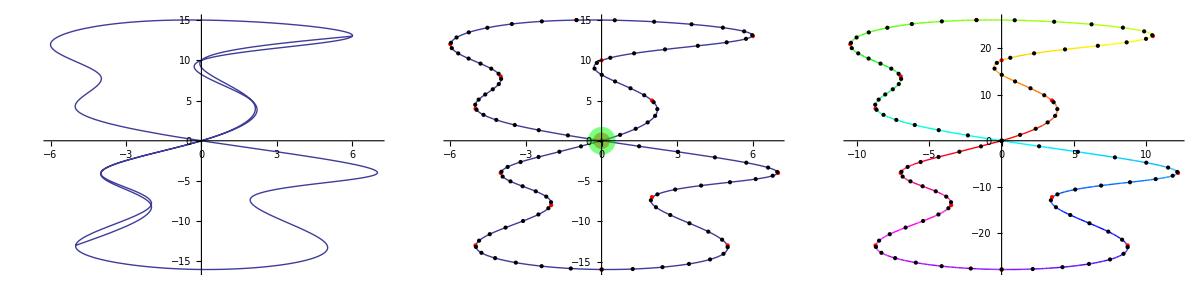

{{53.8583,3.83693×10^-13},170.305,3.41061×10^-13,{45.7141,54.2859},{22.857,27.143},{0.0000463765,3.14136}}

```mathematica
curgen[1,{{0,0},{2,5},{0,10},{6,13},{-1,15},{-6,12},{-4,8},{-5,4},{0,0},{7,-4},{2,-7},{5,-13},{0,-16},{-5,-13},{-2,-8},{-4,-4}},12]
```

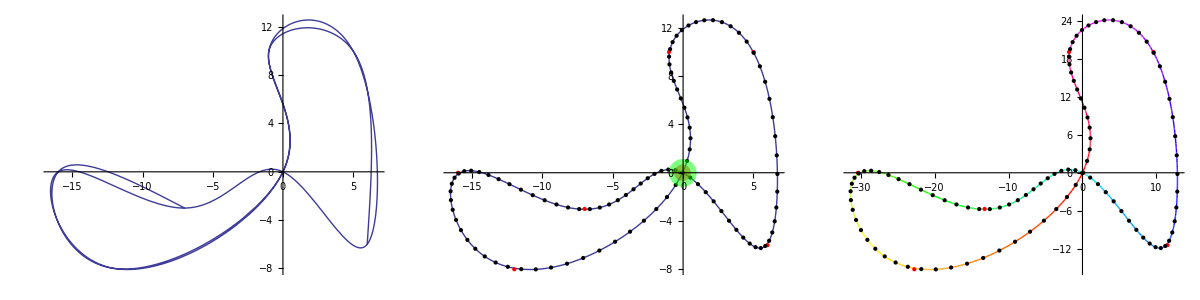

{{-82.7692,1.27898×10^-13},166.003,-1.13687×10^-13,{43.4134,56.5866},{21.7067,28.2933},{-0.000157813,3.13966}}

```mathematica
curgen[2,{{0,0},{-12,-8},{-16,0},{-7,-3},{0,0},{6,-6},{5,10},{-1,10}}]
```

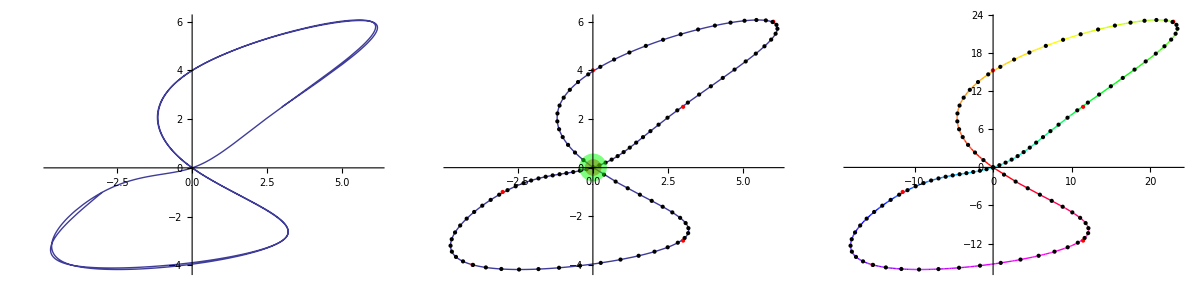

{{-31.9207,1.7053×10^-13},149.648,1.13687×10^-13,{47.4598,52.5402},{23.7299,26.2701},{0.000595718,3.14109}}

```mathematica
curgen[3,{{0,0},{0,4},{6,6},{3,5/2},{0,0},{-3,-1},{-4,-4},{3,-3}},5]
```

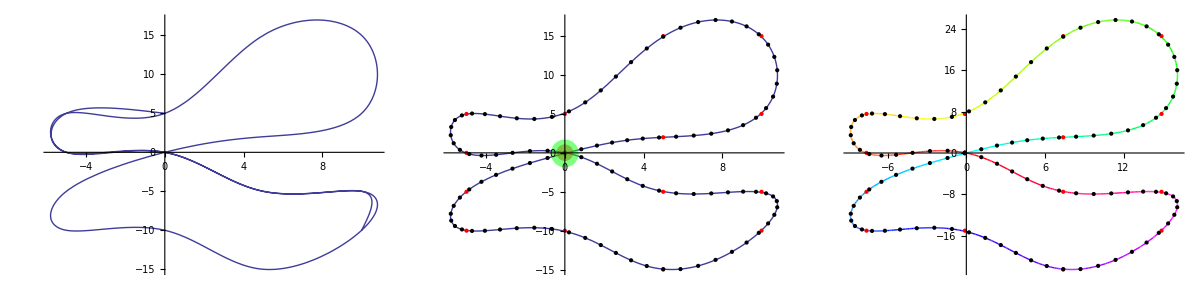

{{13.0682,7.4607×10^-14},158.315,-3.41061×10^-13,{51.0399,48.9601},{25.52,24.48},{-0.00553941,3.13585}}

```mathematica
curgen[4,{{0,0},{-5,0},{-5,5},{0,5},{5,15},{10,15},{10,5},{5,2},{0,0},{-5,-5},{-5,-10},{0,-10},{5,-15},{10,-10},{10,-5},{5,-5}},10]
```

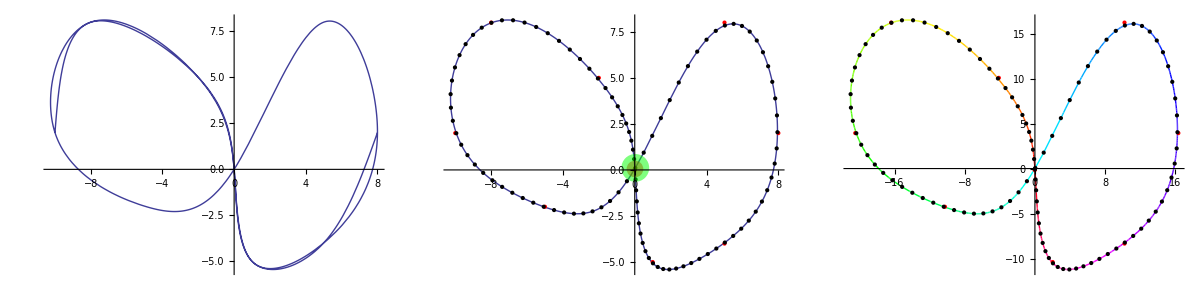

{{-16.0643,-4.54747×10^-13},134.024,-1.13687×10^-13,{51.2784,48.7216},{25.6392,24.3608},{0.00285216,3.13874}}

```mathematica
curgen[5,{{0,0},{-2,5},{-8,8},{-10,2},{-5,-2},{0,0},{5,8},{8,2},{5,-4},{1,-5}}]
```

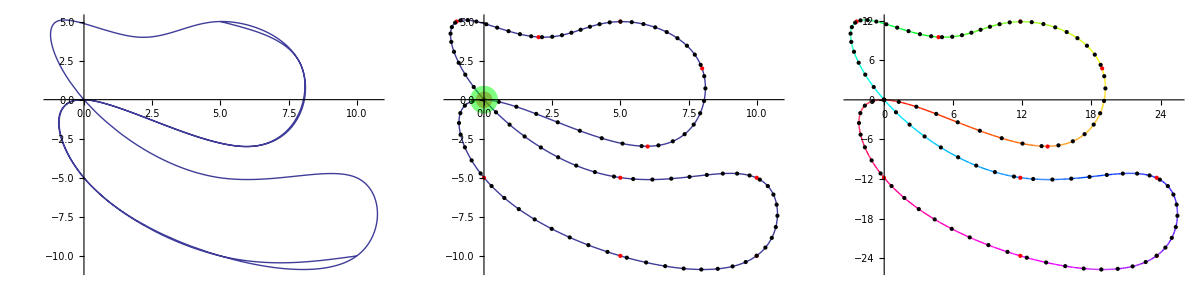

{{28.5557,-3.75451×10^-11},153.953,-1.13687×10^-13,{47.7276,52.2724},{23.8638,26.1362},{0.000358411,3.14263}}

```mathematica
curgen[6,{{0,0},{6,-3},{8,2},{5,5},{2,4},{-1,5},{0,0},{5,-5},{10,-5},{10,-10},{5,-10},{0,-5}},10]
```

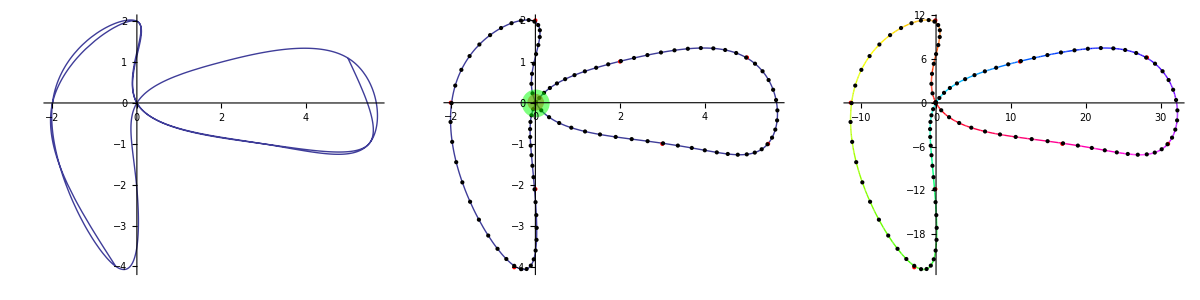

{{48.1454,-4.53326×10^-12},155.382,0.,{46.1687,53.8313},{23.0844,26.9156},{-0.00461697,3.14737}}

```mathematica
curgen[7,{{0,0},{0,2},{-2,0},{-1/2,-4},{0,-2.1},{0,0},{2,1},{5,1.1},{5.5,-1},{3,-1}},6]
```

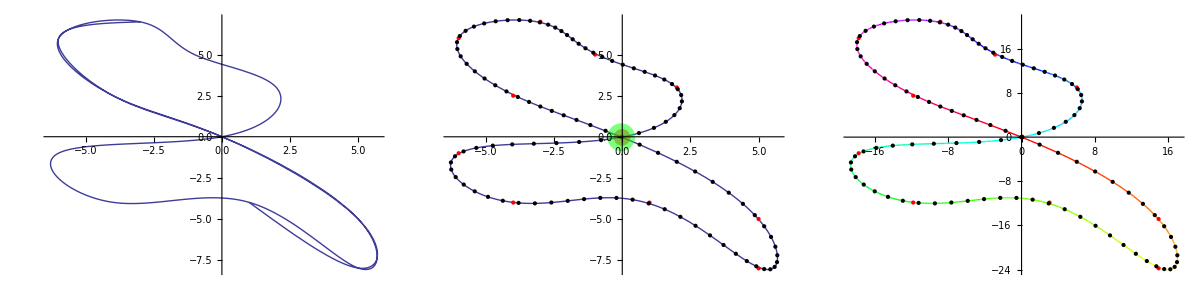

{{54.7399,1.68541×10^-11},163.549,1.13687×10^-13,{54.3561,45.6439},{27.178,22.822},{-0.00178339,3.14291}}

```mathematica
curgen[8,{{0,0},{5,-5},{5,-8},{1,-4},{-4,-4},{-6,-1},{0,0},{2,3},{-1,5},{-3,7},{-6,6},{-4,2.5}},7]
```

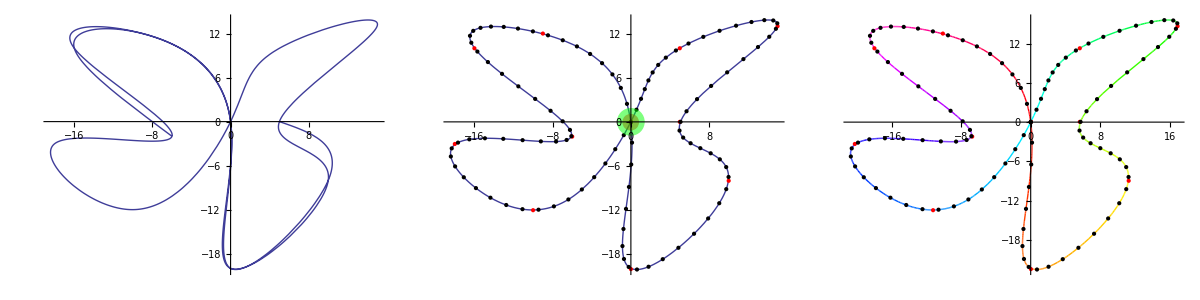

{{24.4367,-1.77153×10^-10},191.592,3.41061×10^-13,{48.0554,51.9446},{24.0277,25.9723},{-0.000262402,3.14288}}

```mathematica
curgen[9,{{0,0},{0,-20},{10,-8},{5,0},{15,13},{5,10},{0,0},{-10,-12},{-18,-3},{-6,-2},{-16,10},{-9,12}},8]
```

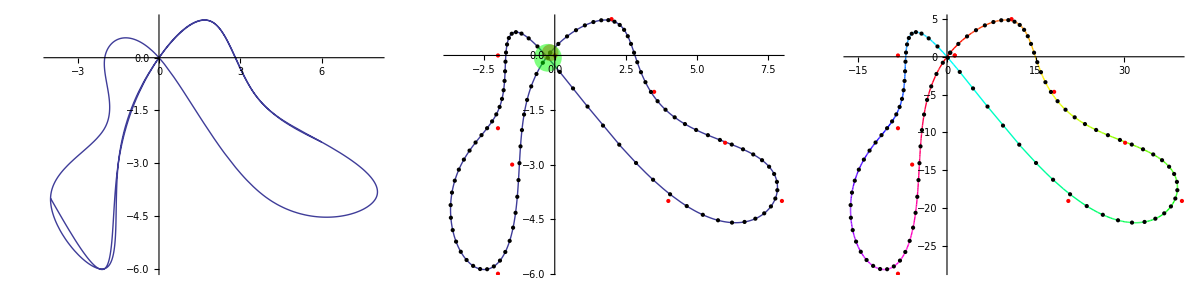

{{162.608,-5.68434×10^-14},174.847,-1.13687×10^-13,{62.9399,37.0601},{31.4699,18.5301},{-0.0262501,3.14657}}

```mathematica
curgen[10,{{0,0},{2,1},{7/2,-1},{6,-2.4},{8,-4},{4,-4},{0,0},{-2,0},{-2,-2},{-4,-4},{-2,-6},{-3/2,-3}}]
```

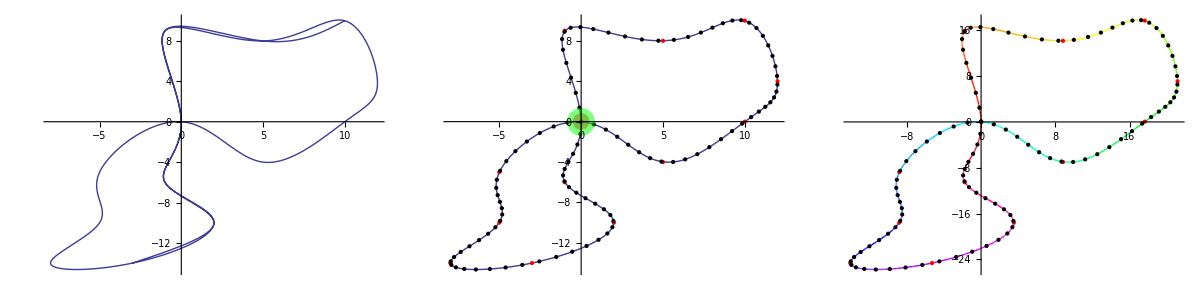

{{182.353,-1.98952×10^-13},151.896,1.13687×10^-13,{64.5112,35.4888},{32.2556,17.7444},{-0.00206023,3.14141}}

```mathematica
curgen[11,{{0,0},{-1,9},{5,8},{10,10},{12,4},{10,0},{5,-4},{0,0},{-5,-5},{-5,-10},{-8,-14},{-3,-14},{2,-10},{-1,-6}},10]
```

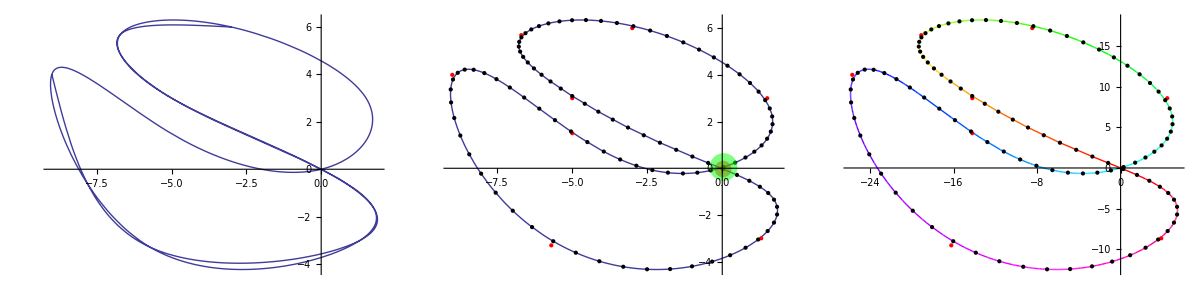

{{-119.89,-2.41585×10^-13},151.201,1.13687×10^-13,{40.4595,59.5405},{20.2297,29.7703},{0.0108097,3.15696}}

```mathematica
curgen[12,{{0,0},{-5,3},{-6.7,5.7},{-3,6},{1.5,3},{0,0},{-5,1.5},{-9,4},{-5.7,-3.3},{1.3,-3}},5]
```

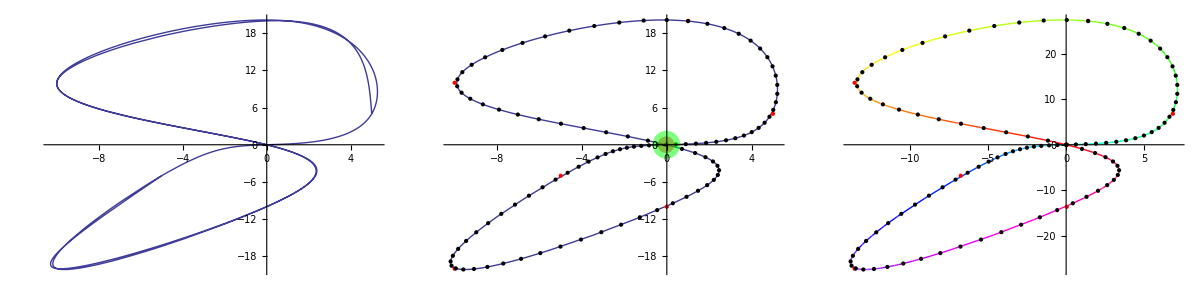

{{202.213,2.55795×10^-13},142.6,-2.27374×10^-13,{66.0916,33.9084},{33.0458,16.9542},{-0.000114623,3.14338}}

```mathematica
curgen[13,{{0,0},{-10,10},{1,20},{5,5},{0,0},{-5,-5},{-10,-20},{0,-10}}]
```

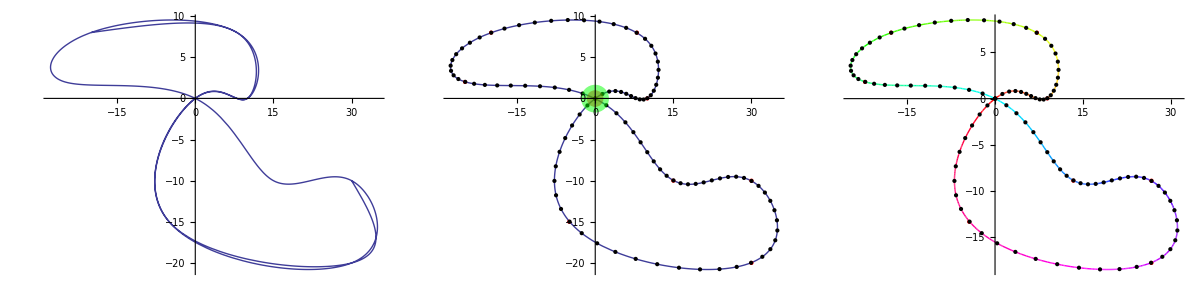

{{176.172,-8.52651×10^-14},169.652,0.,{35.9806,64.0194},{17.9903,32.0097},{-0.000605481,3.14139}}

```mathematica
curgen[14,{{0,0},{10,0},{8,8},{-20,8},{-25,2},{0,0},{15,-10},{30,-10},{30,-20},{-5,-15}},8]
```

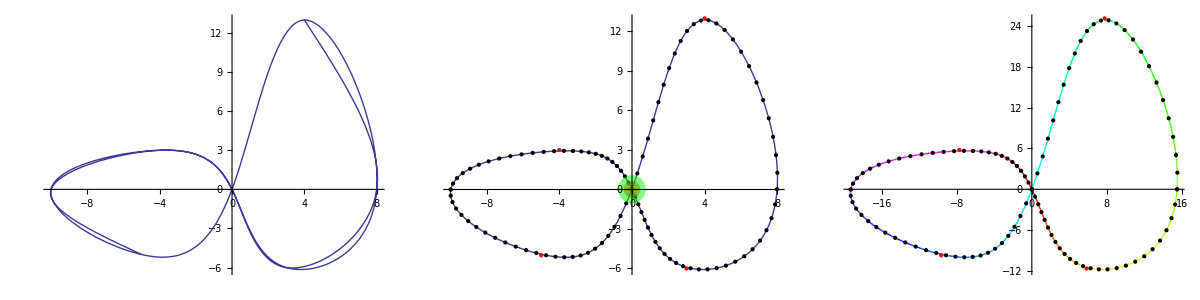

{{-176.279,0.},139.082,-1.13687×10^-13,{64.0279,35.9721},{32.0139,17.9861},{-0.00127873,3.14206}}

```mathematica
curgen[15,{{0,0},{3,-6},{8,0},{4,13},{0,0},{-5,-5},{-10,0},{-4,3}}]
```

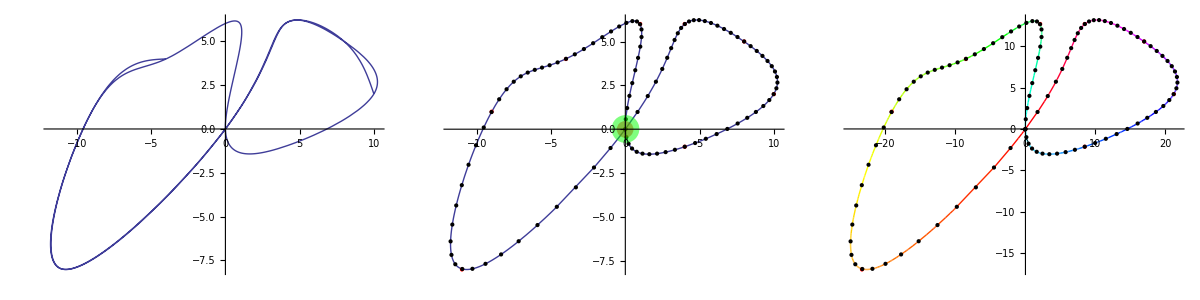

{{202.381,-2.6148×10^-12},145.901,-1.13687×10^-13,{66.1049,33.8951},{33.0525,16.9475},{-0.00151243,3.14122}}

```mathematica
curgen[16,{{0,0},{-11,-8},{-9,1},{-4,4},{1,6},{0,0},{4,-1},{10,2},{8,5},{4,6}},8]
```

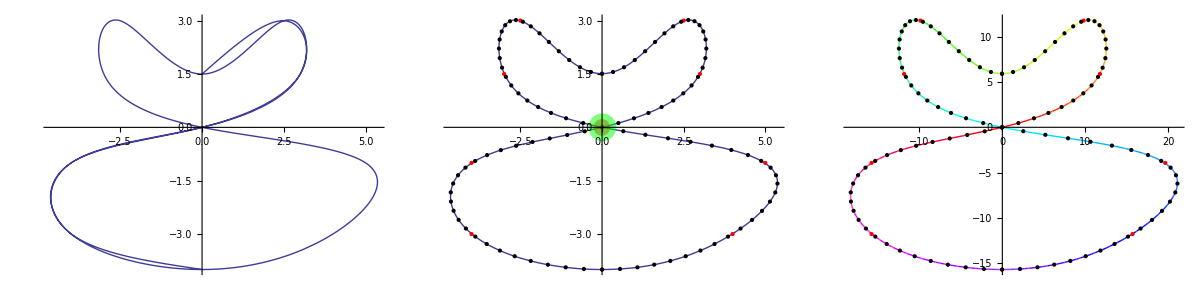

{{287.866,-1.45519×10^-11},155.516,1.13687×10^-13,{27.0924,72.9076},{13.5462,36.4538},{0.00176301,3.14141}}

```mathematica
curgen[17,{{0,0},{3,1.5},{2.5,3},{0,1.5},{-2.5,3},{-3,1.5},{0,0},{5,-1},{4,-3},{0,-4},{-4,-3},{-4,-1}},8]
```

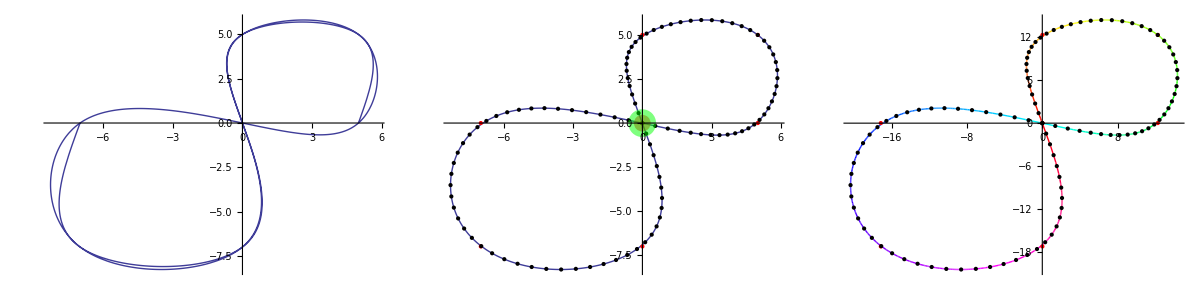

{{-205.076,-8.52651×10^-14},125.33,0.,{33.6806,66.3194},{16.8403,33.1597},{0.000118866,3.14104}}

```mathematica
curgen[18,{{0,0},{0,5},{5,5},{5,0},{0,0},{-7,0},{-7,-7},{0,-7}},5]
```

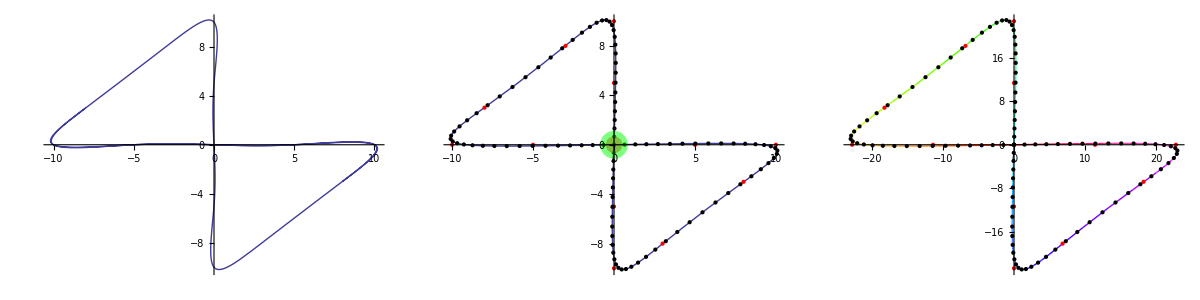

{{1.32254×10^-13,-9.51195×10^-14},156.218,-1.13687×10^-13,{50.,50.},{25.,25.},{0.,3.14159}}

```mathematica
curgen[19,{{0,0},{-5,0},{-10,0},{-8,3},{-3,8},{0,10},{0,5},{0,0},{0,-5},{0,-10},{3,-8},{8,-3},{10,0},{5,0}},5]
```

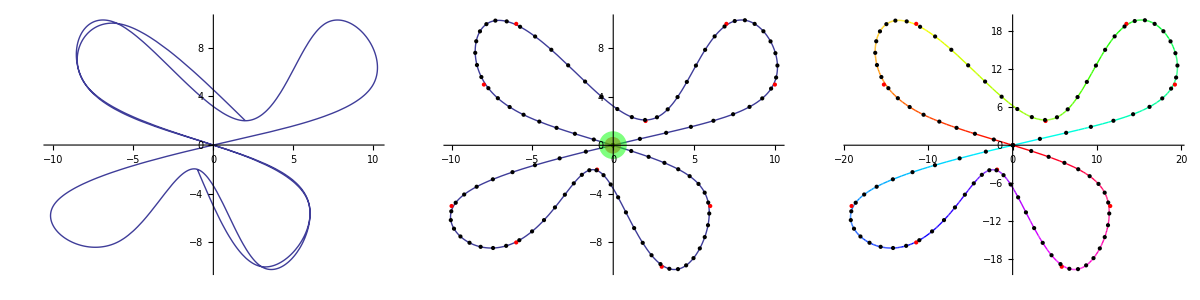

{{41.6492,-2.50964×10^-11},203.868,1.13687×10^-13,{53.3143,46.6857},{26.6572,23.3428},{0.000519045,3.14218}}

```mathematica
curgen[20,{{0,0},{-8,5},{-6,10},{2,2},{7,10},{10,5},{0,0},{-10,-5},{-6,-8},{-1,-2},{3,-10},{6,-5}},7]
```

```mathematica
(*Block[{cb,cow},
cb={{0,0},{0,5},{0,10},{-1,15},{-5,16},{-12,16},{-12,22},{-8,25},{-8,30},{-11,32},
{-19,32},{-22,30},{-22,25},{-18,22},{-18,16},{-25,16},{-29,15},{-30,10},{-30,5},{-30,0},{-25,0},{-20,0},{-15,0},{-10,0},{-5,0}};
cow=Join[cb,-Reverse[cb]];

curgen[21,cow,18]//Quiet

]*)
```

#### ensembles

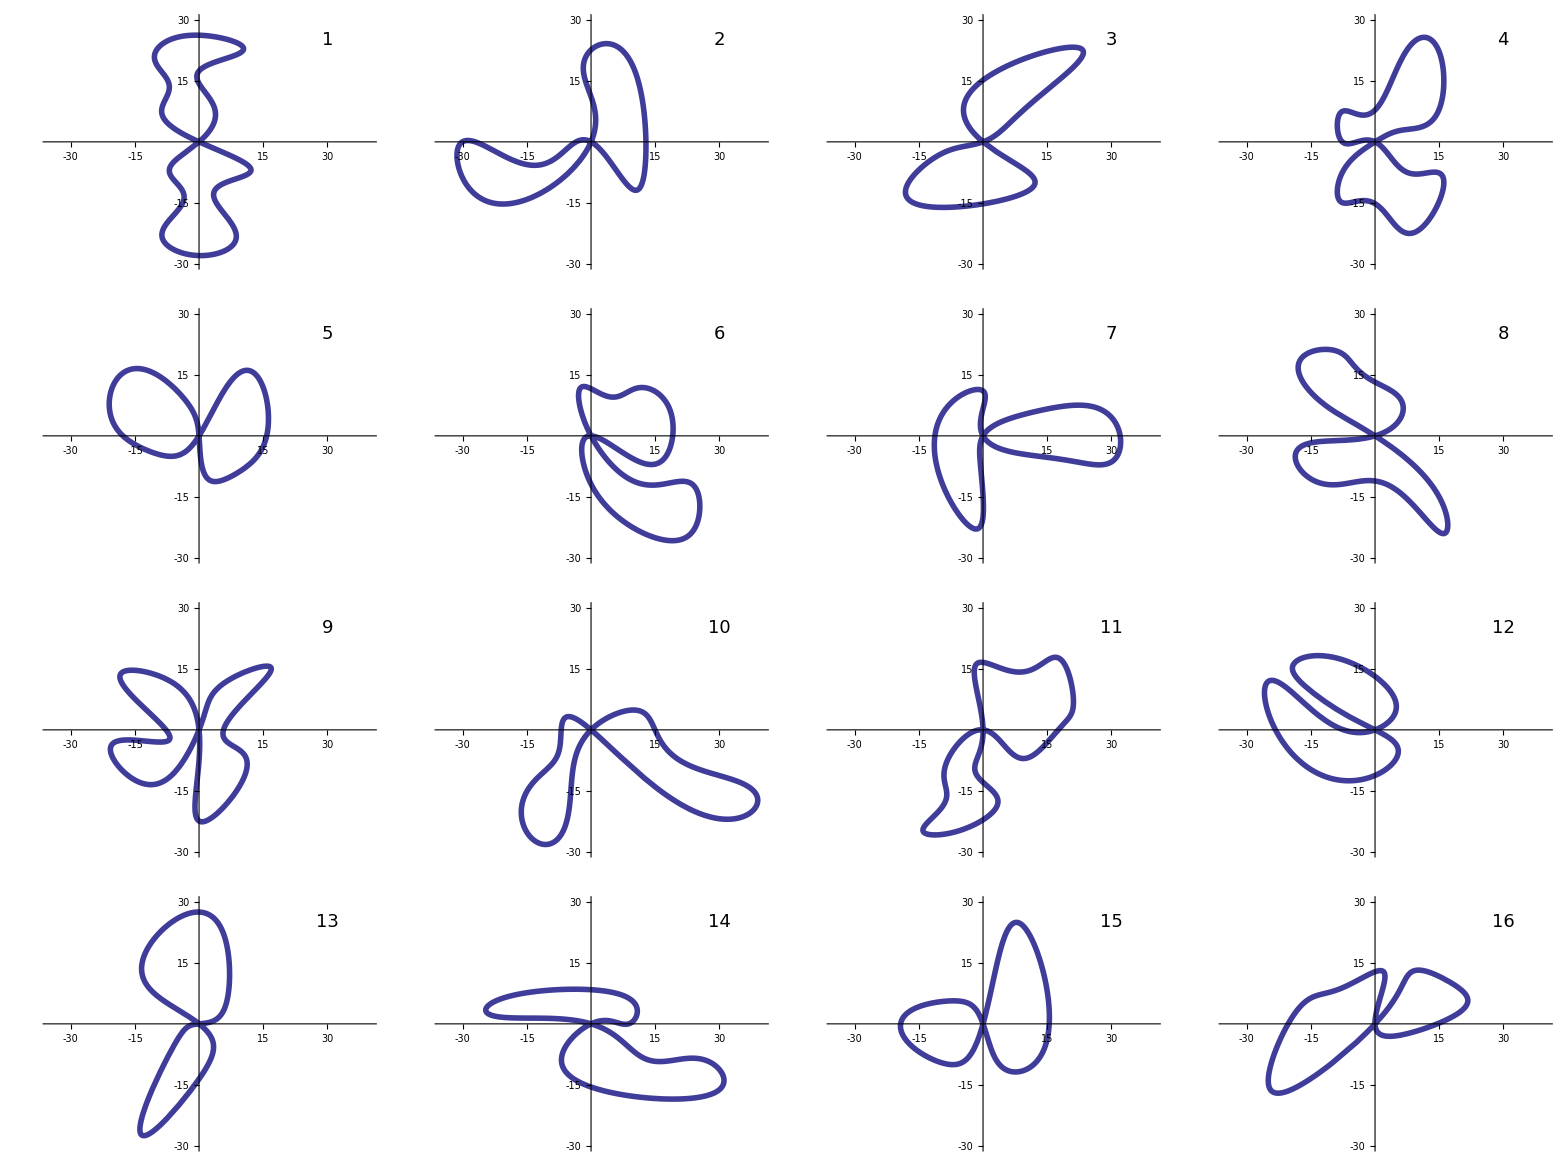
y | -Graphics-
 | x

```mathematica
Block[{iniplots},
iniplots=
Framed@Labeled[
TableForm[
Block[{columns=4,rows=4,n,i,j},
n=columns(i-1)+j;
Table[
ParametricPlot[Subscript[curve, n][u],{u,0,2π},
PlotStyle->Thickness[.01],
PlotRange->{{-35,40},{-30,30}},
Epilog->Text[Style[n,18],{30,25}],Ticks->{{-30,-15,15,30},{-30,-15,15,30}},
AxesStyle->Arrowheads[Automatic]
],{i,1,rows},{j,1,columns}
]
]
],{Style[y,labfontsize,labfontthickness],Style[x,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];
Export["plots/1InitialCurvePlots.eps",iniplots];
Export["/home/julian/latex/thesis/1InitialCurves.eps",iniplots];
iniplots
]
```

```mathematica
nmax=17;
Subscript[elist, 1]=Range[1,nmax];
Subscript[elist, 2]={11,8,13,3,7,4,2,6,10,9,5,12,14,1,15,16,17};
Subscript[elist, 3]={4,3,12,14,13,11,8,6,5,2,15,1,7,10,9,16,17};
```

## curve evolution & fits

### functions

#### plotting

```mathematica
Clear[lineplot3d,evoplot3d,evointplot3d,evocomplot3d,distdistplot];

lineplot3d[sol_List,scale_,maxtime_,opts___]:=
Module[{plots,n,t1,t2},

n=Length[sol]/2-1;
{t1,t2}=First[First[sol][[2]][[1]]];
(*If[t2≤99&&t2>1,t2=t2-1];*)
If[t2≠maxtime,t2=t2-1];

plots=Table[{ Subscript[x, i][t]/.sol[[i+1]],Subscript[y, i][t]/.sol[[i+n+2]],t/scale},{i,1,n,2}
];
ParametricPlot3D[plots//Evaluate,{t,t1,t2},AspectRatio->1,PerformanceGoal->"Speed",opts]
];

evoplot3d[num_,scale_:2,tfinal_:1000,opts___]:=
Module[{maxtime,sol,n,tmax,t0,n0,curplot,lineplots},
If[tfinal>Subscript[Tmax, num],maxtime=Subscript[Tmax, num],maxtime=tfinal];
sol=Subscript[solution, num];
n=Length@sol;
tmax=First[First[sol[[n]]][[2]]][[1]][[2]];
t0=First[First[sol[[1]]][[2]]][[1]][[2]];
If[t0==1,n0=2,n0=1];

curplot=ParametricPlot3D[{Flatten@{ Subscript[curve, num][u],0},{0,0,tmax/scale}},{u,0,2π},(*ColorFunction->Function[{x,y,z,u},Hue[u]],*)PlotRange->All,PlotStyle->{{Black,Thick},{White,Thin}},opts];
lineplots=Table[lineplot3d[sol[[i]],scale,maxtime,Boxed->False,Axes->True,PlotStyle->{{RGBColor[0,0,.4],Thin}}],{i,n0,n}];

Show[curplot,lineplots]
];

evointplot3d[num_,scale_:2,tfinal_:1000,opts___]:=
Show[
evoplot3d[num,scale,tfinal,opts],
ParametricPlot3D[Flatten[{ Subscript[i, num][t],t/scale}],{t,0,Subscript[Tmax, num]},PlotStyle->{Red,Thickness[.01]}]
];

evocomplot3d[num_,scale_:2]:=
Show[
evoplot3d[num,scale],
ParametricPlot3D[Flatten[{scale Subscript[com, num][t],t}],{t,0,Subscript[Tmax, num]},PlotStyle->{Red,Thick},PerformanceGoal->"Speed"]
];

distdistplot[num_,t_]:=
Module[{sol=Subscript[solution, num],X,Y,n,dist,i,j,pmin=10,sorteddist},

{X,Y}=coordselect[sol,t];
n=Length@X-1;

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],j-i,{i,j}}]
];
];
];

sorteddist=SortBy[dist[[2,1,All]],First];
ListPlot[sorteddist[[All,{2,1}]]]
];
```

#### initial grid points

```mathematica
Clear[grdpts];

grdpts[num_Integer,n_Integer:150]:=
Block[{pts},
pts=Thread[Subscript[curve, num][2π Range[0,n]/n]];
Table[{2π i/n,pts[[i+1]]},{i,0,n}]
];
```

#### process equation

```mathematica
Clear[proequ];

proequ[t0_:0,icpts_List]:=
Module[{n,grdpts,ugrid,X,Y,xu,xuu,yu,yuu,v,xeqns,yeqns,ic,xic,yic},

n=Length[icpts]-1;
grdpts=Range[0,n];
ugrid=icpts[[All,1]];

X[t_]=Through[Thread[Subscript[x, grdpts]][t]];
Y[t_]=Through[Thread[Subscript[y, grdpts]][t]];

xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,X[t]];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,Y[t]];
xuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,X[t]];
yuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,Y[t]];
v=Sqrt[xu^2+yu^2];

xeqns = Thread[D[X[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)xu+xuu)];
yeqns = Thread[D[Y[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)yu+yuu)];

ic=Flatten@Table[Thread[{Subscript[x, i][t0],Subscript[y, i][t0]}==icpts[[i+1,2]]],{i,0,n}];

First[
NDSolve`ProcessEquations[
Join[xeqns,yeqns,ic],
Join[Thread[Subscript[x, grdpts]],Thread[Subscript[y, grdpts]]],
t]
]

];
```

#### fit

```mathematica
Clear[fit];

fit[sol_List,idA_]:=
Module[{n,t1,t2,grid,X1,Y1,X2,Y2,fddf,
dist,dmin,dmax,l1,l2,l,i,j,d,
u,newdist,nnew,newX,newY,newgrid,
xmdp,ymdp,order=14,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,fc,da},

{t1,t2}=First[First[sol][[2]]][[1]]-{0,1};
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
dist=Sqrt[fddf[X1]^2 +fddf[Y1]^2];
l1=Total[Drop[dist,1]];
dmin=.8Min@dist;
dmax=Max@dist;

X2=Through[Thread[Subscript[x, grid]][t2]]/.sol;
Y2=Through[Thread[Subscript[y, grid]][t2]]/.sol;
dist=Sqrt[fddf[X2]^2 +fddf[Y2]^2];
l2=Total[Drop[dist,1]];

newdist=Reap[
For[i=1;j=0,i≤ n,i++,
d=Sum[dist[[m]],{m,j+1,i}];
If[i==n,Sow[{i,d}];Break[],None,Print["Error while fitting: Break at i=n"]];
If[d≥ dmin,j=i;Sow[{i,d}],None,Print["Error while fitting: Sow for d>dmin"]];
];
][[2,1]];
nnew=Length[newdist];

If[l2!=Total[newdist[[All,2]]],Print["Error after fitting: Fitted length unequal original length"];
];

Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+newdist[[i,2]],{i,1,nnew}];

newX=Through[Thread[Subscript[x, newdist[[All,1]]]][t2]]/.sol;
newY=Through[Thread[Subscript[y, newdist[[All,1]]]][t2]]/.sol;
newgrid=Table[{2π Subscript[l, i]/l2,{newX[[i]],newY[[i]]}},{i,1,nnew}];
newgrid=Prepend[newgrid,{0,Last[newgrid][[2]]}];

xmdp=Table[{newgrid[[i,1]],newgrid[[i,2,1]]},{i,1,nnew+1}];
ymdp=Table[{newgrid[[i,1]],newgrid[[i,2,2]]},{i,1,nnew+1}];

xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xmdp,xexp[u],xpara ,u];
yfitdat=FindFit[ymdp,yexp[u],ypara ,u];

fc[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

da=1/2NIntegrate[Evaluate[(fc[u][[2]])( D[fc[u][[1]], u])-(fc[u][[1]])(D[fc[u][[2]], u])],{u,0,2π},AccuracyGoal->8];

Print["  t=",t2,", Fit: curve length dev: ",100(NIntegrate[Evaluate[Sqrt[(D[fc[u], u]).(D[fc[u], u])]],{u,0,2π}]-l2)/l2,
"%.",{da,idA,da-idA,If[idA>10^-6,(1-Abs[da/idA]),"area differnce < 10^-16"]100,dmin,dmax,nnew,l2}
];

{da,Table[{2π i/ nnew,fc[2π i/nnew]},{i,0,nnew}]}

];
```

#### evolution

```mathematica
Clear[evolution];

evolution[num_Integer,n_:300,print_:False]:=
Module[{grid,state,dt,sol,inidiffA,er,erp,tdummy,t},

inidiffA=diffA[num];
Subscript[solution, num]={};

grid=grdpts[num,n];
state=proequ[0,grid];

For[t=0,t<80,t++,
NDSolve`Iterate[state,t];
sol=NDSolve`ProcessSolutions[state];

If[Chop[Abs@inidiffA,10^-6]>0,
er=Abs[10^6(1-areadiff[sol,t]/inidiffA)];,
er=Abs[10^6(inidiffA-areadiff[sol,t])];
];
(*erp=10^6(-(∂_tdummy areadiff[sol,tdummy])/.tdummy->t)/inidiffA;*)

If[
er≥2,
Print["t=",t,", error tolerance exceeded: error=",NumberForm[er ,2](*,",  error derivative=",NumberForm[erp ,2]*)
];
Subscript[solution, num]=Append[Subscript[solution, num],sol];
Block[{t1,t2,newinidiffA,newgrid,newstate,newsol,newer1,newer2,newerp1,newerp2},
{t1,t2}=First[First[sol][[2]]][[1]];
{newinidiffA,newgrid}=fit[sol,inidiffA];
inidiffA=newinidiffA;
newstate=proequ[t2-1,newgrid];
NDSolve`Iterate[newstate,t2];
newsol=NDSolve`ProcessSolutions[newstate];

If[Chop[Abs@inidiffA,10^-6]>0,
newer1=Abs[10^6(1-areadiff[newsol,t2-1]/inidiffA)];
newer2=Abs[10^6(1-areadiff[newsol,t2]/inidiffA)];
newerp1=10^6(-(D[areadiff[newsol,tdummy], tdummy])/.tdummy->(t-1))/inidiffA;
newerp2=10^6(-(D[areadiff[newsol,tdummy], tdummy])/.tdummy->t)/inidiffA;,
newer1=Abs[10^6(inidiffA-areadiff[newsol,t2-1])];
newer2=Abs[10^6(inidiffA-areadiff[newsol,t2])];
newerp1=10^6(-(D[areadiff[newsol,tdummy], tdummy])/.tdummy->(t-1));
newerp2=10^6(-(D[areadiff[newsol,tdummy], tdummy])/.tdummy->t);
];

If[newer2≥ 2,
Print["t=",Subscript[Tmax, num]=t2,", Abort: error tolerance exceeded after fit,  error = ",newer2, " (",newer1,",  error derivative = ",newerp2," (",newerp1")"];
Abort[];
];
state=newstate;
];,

If[print,
Print["t=",t,",  error=",NumberForm[er ,2] (*,",  error derivative=",NumberForm[erp ,2]*)
]
];
];
];

];
```

#### discrete: areadifference, length

```mathematica
Clear[areadiff,length];

areadiff[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[fddf[X]Y -fddf[Y]X,1]]/2

];

length[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[Sqrt[fddf[X]^2 +fddf[Y]^2],1]]

];
```

#### coord/index selection (input: solutions & time, output: coords {x,y}/index according time)

```mathematica
Clear[coordselect,indexselect];

coordselect[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
grid=Range[0,Length[sol[[i]]]/2 -1];
X=Through[Thread[Subscript[x, grid]][t]]/.sol[[i]];
Y=Through[Thread[Subscript[y, grid]][t]]/.sol[[i]];
{X,Y}
];

indexselect[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
i
];
```

#### (fufu: length, area, intersection)

```mathematica
Clear[flength,fareadiff,farea,intersection];
flength[num_Integer,t_]:=
Module[{sol,i},
sol=Subscript[solution, num];
i=indexselect[sol,t];
length[sol[[i]],t]
];

fareadiff[num_Integer,t_]:=
Module[{sol,i},
sol=Subscript[solution, num];
i=indexselect[sol,t];
areadiff[sol[[i]],t]
];

farea[num_Integer,t_,denom_:4]:=
Module[{sol=Subscript[solution, num],X,Y,n,pmin,dist,n1,n2,i,j,fddf,alist},

{X,Y}=coordselect[sol,t];
n=Length@X-1;
pmin=IntegerPart[n/denom];

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],j-i,{i,j}}]
];
];
];
If[dist[[2]]=={},Print["Intersection error: empty list. t=",t];Abort[];];
{n1,n2}=SortBy[dist[[2,1,All]],First][[1,3]]+1;

fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];
alist=(fddf[X]Y -fddf[Y]X)/2;

(*Print[
ListPlot[Table[{X[[k]],Y[[k]]},{k,1,n}],Epilog->{Red,Opacity[.5],PointSize[Medium],Point[{{X[[n1]],Y[[n1]]},{X[[n2]],Y[[n2]]}}]}
]
];*)

Abs@Total[Take[alist,{n1,n2-1}]]+Abs@Total[Join[Take[alist,{n2,n}],Take[alist,{1,n1-1}]]]

];

intersection[num_Integer,t_,denom_:3,plot_:False,opts___]:=
Module[{sol=Subscript[solution, num],X,Y,n,pmin,dist,i,j,sorteddist,n1,n2,spline1,spline2,u1,u2,u,p},

{X,Y}=coordselect[sol,t];
n=Length@X-1;
pmin=IntegerPart[n/denom];

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],j-i,{i,j}}]
];
];
];
If[dist[[2]]=={},Print["Intersection error: empty list. t=",t];Abort[];];

sorteddist=SortBy[dist[[2,1,All]],First];
{n1,n2}=sorteddist[[1,3]]+1;

spline1=SplineFit[Table[{Drop[X,-1][[Mod[n1+i,n,1]]],Drop[Y,-1][[Mod[n1+i,n,1]]]},{i,-4,4}],Cubic];
spline2=SplineFit[Table[{Drop[X,-1][[Mod[n2+i,n,1]]],Drop[Y,-1][[Mod[n2+i,n,1]]]},{i,-4,4}],Cubic];
{u1,u2}={u,p}/.FindRoot[Thread[spline1[u]==spline2[p]],{{u,4,0,8},{p,4,0,8}}];

If[plot==True,
Print@ParametricPlot[{spline1[u],spline2[u]},{u,0,8},Epilog->{{Green,PointSize[Large],Opacity[0.5],Point[spline1[u1]]},{Black,Point[spline2[u2]]}},opts];
];

spline1[u1]
];

centroid[num_,t_]:=
Module[{X,Y,n,fddf,v,l},
{X,Y}=coordselect[Subscript[solution, num],t];
n=Length@X-1;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n],DifferenceOrder->6];
v=Sqrt[fddf[X]^2 +fddf[Y]^2];
l=Total[Drop[v,1]];

{Total[Drop[X v,1] ],Total[Drop[Y v,1]]}/l

];
```

#### fufu: multifu

```mathematica
Clear[fmulti];

fmulti[num_Integer,t_,denom_:4]:=
Module[{sol=Subscript[solution, num],X,Y,n,pmin,dist,i,j,n1,n2,spline1,spline2,u1,u,p,fddf,v,l,alist},

{X,Y}=coordselect[sol,t];
n=Length@X-1;
pmin=IntegerPart[n/denom];

dist=Reap[
For[i=0,i<n,i++,
For[j=i+pmin,(j<n && i>pmin) ∨ (j<n-pmin+i && i≤pmin),j++,
Sow[{Sqrt[(X[[i+1]]-X[[j+1]])^2+(Y[[i+1]]-Y[[j+1]])^2],{i,j}}]
];
];
];
If[dist[[2]]=={},Print["Intersection error: empty list. t=",t];Abort[];];
{n1,n2}=SortBy[dist[[2,1,All]],First][[1,2]]+1;

spline1=SplineFit[Table[{Drop[X,-1][[Mod[n1+i,n,1]]],Drop[Y,-1][[Mod[n1+i,n,1]]]},{i,-4,4}],Cubic];
spline2=SplineFit[Table[{Drop[X,-1][[Mod[n2+i,n,1]]],Drop[Y,-1][[Mod[n2+i,n,1]]]},{i,-4,4}],Cubic];
u1=u/.FindRoot[Thread[spline1[u]==spline2[p]],{{u,4,0,8},{p,4,0,8}},AccuracyGoal->8,MaxIterations->200];


fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];
alist=(fddf[X]Y -fddf[Y]X)/2;
v=Sqrt[fddf[X]^2 +fddf[Y]^2];
l=Total[Drop[v,1]];

{
Total[Drop[Sqrt[fddf[X]^2 +fddf[Y]^2],1]],Abs@Total[Take[alist,{n1,n2-1}]]+Abs@Total[Join[Take[alist,{n2,n}],Take[alist,{1,n1-1}]]],
spline1[u1],
{Total[Drop[X v,1] ],Total[Drop[Y v,1]]}/l
}

];
```

#### fufufits

```mathematica
Clear[fullfits];

fullfits[num_Integer,denom_:4,fitpts_:100,lorder_:12,aorder_:8,intorder_:12,comorder_:12,lengtherrormagnification_:100,areaerrormagnification_:100]:=
Module[{tmax=Subscript[Tmax, num]-1,tab,t},
Subscript[fd, num]=denom;
Print[num];
tab=Table[Flatten[{tmax i/fitpts,fmulti[num,tmax i/fitpts,denom]}],{i,0,fitpts}];

Subscript[l, num][t_]=Fit[tab[[All,{1,2}]],Thread[t^Range[0,lorder]],t];
Subscript[a, num][t_]=Fit[tab[[All,{1,3}]],Thread[t^Range[0,aorder]],t];
Subscript[i, num][t_]={Fit[tab[[All,{1,4}]],Thread[t^Range[0,intorder]],t],Fit[tab[[All,{1,5}]],Thread[t^Range[0,intorder]],t]};
Subscript[com, num][t_]={Fit[tab[[All,{1,6}]],Thread[t^Range[0,comorder]],t],Fit[tab[[All,{1,7}]],Thread[t^Range[0,comorder]],t]};

{
{{"n     =",num},{"fd    =",denom},{"FitPts=",fitpts},{"O(L)  =",lorder},{"O(A)  =",aorder},{"O(I)  =",intorder},{"O(COM)=",comorder},{"LErMag)=",lengtherrormagnification},{"AErMag)=",areaerrormagnification}},Show[ErrorBarPlots`ErrorListPlot[Table[{{tmax jj/fitpts,tab[[jj+1,2]]},ErrorBar[lengtherrormagnification Abs[Subscript[l, num][tmax jj/fitpts]-tab[[jj+1,2]]]]},{jj,0,fitpts}],PlotLabel->"Length",PlotRange->Full],Plot[Subscript[l, num][t],{t,0,Subscript[Tmax, num]}]],
Show[ErrorBarPlots`ErrorListPlot[Table[{{tmax jj/fitpts,tab[[jj+1,3]]},ErrorBar[areaerrormagnification Abs[Subscript[a, num][tmax jj/fitpts]-tab[[jj+1,3]]]]},{jj,0,fitpts}],PlotLabel->"Area",PlotRange->Full],Plot[Subscript[a, num][t],{t,0,Subscript[Tmax, num]}]],
Show[ParametricPlot[{Subscript[i, num][t]},{t,0,Subscript[Tmax, num]},PlotLabel->"IntersectionPoint",PlotRange->Full],ListPlot[tab[[All,{4,5}]]]],
ListPlot[Table[{tmax jj/fitpts,100 (Subscript[l, num][tmax jj/fitpts]/tab[[jj+1,2]]-1)},{jj,2,fitpts}],PlotLabel->"Rel.Error:Length",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100( Subscript[a, num][tmax jj/fitpts]/tab[[jj+1,3]]-1)},{jj,2,fitpts}],PlotLabel->"Rel.Error:Area",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100 (Subscript[i, num][tmax jj/fitpts][[1]]/tab[[jj+1,4]]-1)},{jj,2,fitpts}],PlotLabel->"Rel.Error:x-Int",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100( Subscript[i, num][tmax jj/fitpts][[2]]/tab[[jj+1,5]]-1)},{jj,2,fitpts}],PlotLabel->"Rel.Error:y-Int",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100 (Subscript[com, num][tmax jj/fitpts][[1]]/tab[[jj+1,6]]-1)},{jj,2,fitpts}],PlotLabel->"Rel.Error:x-COM",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,100 (Subscript[com, num][tmax jj/fitpts][[2]]/tab[[jj+1,7]]-1)},{jj,2,fitpts}],PlotLabel->"Rel.Error:x-COM",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts,(Subscript[i, num][tmax jj/fitpts][[1]]-tab[[jj+1,4]])},{jj,0,fitpts}],PlotLabel->"Abs.Error:x-Int",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts, (Subscript[i, num][tmax jj/fitpts][[2]]-tab[[jj+1,5]])},{jj,0,fitpts}],PlotLabel->"Abs.Error:y-Int",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts, (Subscript[com, num][tmax jj/fitpts][[1]]-tab[[jj+1,6]])},{jj,0,fitpts}],PlotLabel->"Abs.Error:x-COM",PlotRange->Full],
ListPlot[Table[{tmax jj/fitpts, (Subscript[com, num][tmax jj/fitpts][[2]]-tab[[jj+1,7]])},{jj,0,fitpts}],PlotLabel->"Abs.Error:x-COM",PlotRange->Full]
}

];
```

### evolution

```mathematica
evolution[1]
```

t=2, error tolerance exceeded: error=6.8

t=1., Fit: curve length dev: -0.666847%.{54.1214,53.8583,0.263093,-0.48849,0.217662,0.983203,295,163.892}

t=15, error tolerance exceeded: error=2.1

t=14., Fit: curve length dev: -0.00280193%.{54.1158,54.1214,-0.0055644,0.0102813,0.305242,0.668151,269,126.505}

t=60, error tolerance exceeded: error=5.1

t=59., Fit: curve length dev: 0.0017024%.{54.0977,54.1158,-0.0181809,0.0335962,0.362818,0.490651,133,60.3551}

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

t=65, error tolerance exceeded: error=11000.

t=64., Fit: curve length dev: -0.100955%.{54.1187,54.0977,0.0210219,-0.0388592,0.341691,0.484524,101,45.2544}

t=65., Abort: error tolerance exceeded after fit,  error = 65.5765 (1.98272,  error derivative = 650.665 (-7.14769 )

$Aborted

```mathematica
evolution[2]
```

evolution[2]

```mathematica
evolution[3]
```

evolution[3]

```mathematica
evolution[4]
```

evolution[4]

```mathematica
evolution[5]
```

evolution[5]

```mathematica
evolution[6]
```

evolution[6]

```mathematica
evolution[7]
```

evolution[7]

```mathematica
evolution[8]
```

evolution[8]

```mathematica
evolution[9,500]
```

evolution[9,500]

```mathematica
evolution[10]
```

evolution[10]

```mathematica
evolution[11]
```

evolution[11]

```mathematica
evolution[12]
```

evolution[12]

```mathematica
evolution[13]
```

evolution[13]

```mathematica
evolution[14]
```

evolution[14]

```mathematica
evolution[15]
```

evolution[15]

```mathematica
evolution[16]
```

evolution[16]

```mathematica
evolution[17]
```

evolution[17]

```mathematica
evolution[18]
```

evolution[18]

```mathematica
evolution[19,250]
```

evolution[19,250]

```mathematica
evolution[20]
```

evolution[20]

### fits: length, area & intersection

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

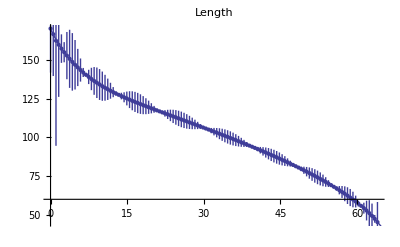
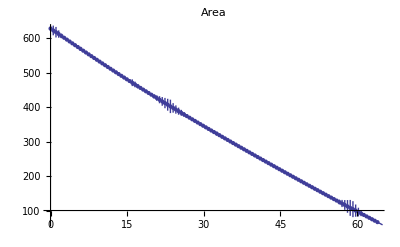
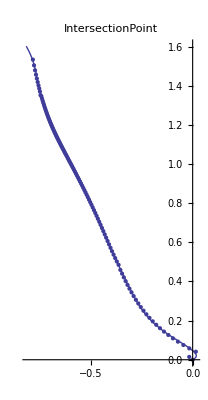
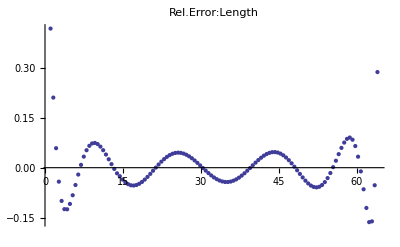
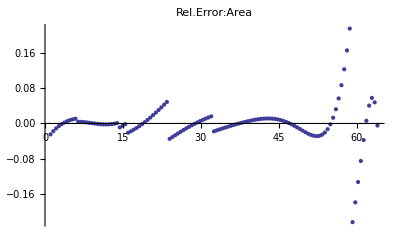
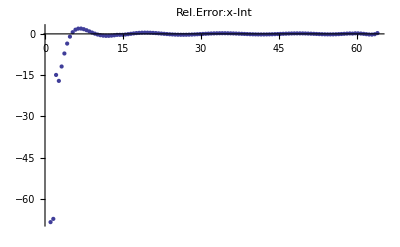
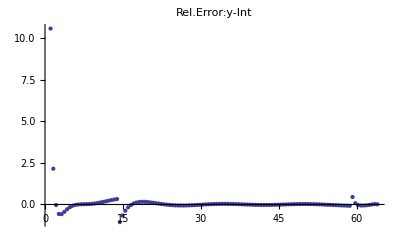
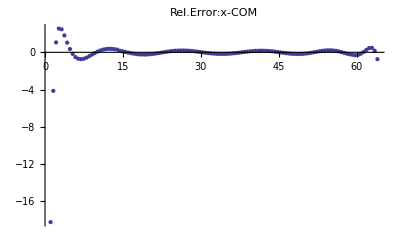
n     = | 1
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 2
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 3
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 4
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 5
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 6
fd    = | 2.6
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 7
fd    = | 4
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 8
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 9
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 10
fd    = | 4
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 11
fd    = | 6
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 12
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 13
fd    = | 5
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 14
fd    = | 4
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 15
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 16
fd    = | 3
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
n     = | 17
fd    = | 5
FitPts= | 120
O(L)  = | 10
O(A)  = | 9
O(I)  = | 12
O(COM)= | 12
LErMag)= | 100
AErMag)= | 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[
{fitpts=120,lorder=10,aorder=9,intorder=12,comorder=12},
TableForm[
Join[
{fullfits[1,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[2,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[3,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[4,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[5,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[6,2.6,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[7,4,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[8,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[9,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[10,4,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[11,6,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[12,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[13,5,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[14,4,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[15,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[16,3,fitpts,lorder,aorder,intorder,comorder]},
{fullfits[17,5,fitpts,lorder,aorder,intorder,comorder]}
]
]
]
```

### plots

#### evolution plots

```mathematica
Block[{evoplot,num=12,rescale=2,time=48,axlabsize=16,ticks,axlabel},
ticks=Ticks->{Automatic,Automatic,{{0,0},{Subscript[Tmax, num]/rescale/2,IntegerPart[Subscript[Tmax, num]/2]},{Subscript[Tmax, num]/rescale,IntegerPart[Subscript[Tmax, num]]}}};
axlabel=AxesLabel->{Style[x,axlabsize+1],Style[y,axlabsize],Style[τ,axlabsize]};

evoplot=
TableForm[{{
evointplot3d[num,rescale,time,ticks,axlabel,AxesEdge->{{-1,-1},{1,-1},{1,1}},ViewPoint->{-.4,-.4,2}],
evointplot3d[num,rescale,time,ticks,axlabel,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ViewPoint->{1.8,-1,2}]
}}];

Export["plots/1EvolutionPlots.eps",evoplot];
Export["/home/julian/latex/thesis/1EvolutionPlots.eps",evoplot];
evoplot
]
```

-Graphics3D- | -Graphics3D-

#### intersection trajectories

```mathematica
Block[{nmax=12,d=8,rescale=4,axlabsize=18,traplots},
traplots=
Show[
Table[
ParametricPlot3D[Flatten[{ Subscript[i, num][t],t/4}],{t,0,Subscript[Tmax, num]},PlotRange->{{-d,d},{-d,d}},Boxed->True,PlotStyle->{Hue[num/nmax],Thickness[.0035]},ViewPoint->{1.3,-2.2,3},Ticks->{Automatic,Automatic,{{0,0},{Subscript[Tmax, 1]/rescale/2,IntegerPart@(Subscript[Tmax, 1]/2)},{Subscript[Tmax, 1]/rescale,IntegerPart@Subscript[Tmax, 1]}}},AxesLabel->{Style[x,axlabsize],Style[y,axlabsize],Style[τ,axlabsize]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}],
{num,1,nmax}
],
Graphics3D[
Prepend[Table[Text[Style[num,14],Flatten[{ Subscript[i, num][Subscript[Tmax, num]],(Subscript[Tmax, num]+2)/4}]],{num,1,nmax}],Point[{0,0,0}]]
]
];
Export["plots/1TrajectoriesOfIntersections.eps",traplots];
Export["/home/julian/latex/thesis/1TrajectoriesOfIntersections.eps",traplots];
traplots
]
```

-Graphics3D-

#### isoperimetric ratio

```mathematica
Block[{columns=4,rows=4},
TableForm[
Table[
Block[{num},
num=columns(ii-1)+jj;
Plot[Subscript[l, num][t]^2/Subscript[a, num][t],{t,0,Subscript[Tmax, num]},PlotRange->{{0,65},{15,50}},PlotLabel->num]
]
,{ii,1,rows},{jj,1,columns}
]
]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

### miscelleneous

#### checks

```mathematica
TableForm[Table[Table[Column[{Subscript[elist, n][[i]],Subscript[Tmax, Subscript[elist, n][[i]]]}],{i,1,nmax}],{n,1,3}]]
```

1
65. | 2
64. | 3
64. | 4
64. | 5
63. | 6
62. | 7
63. | 8
58. | 9
56. | 10
54. | 11
50. | 12
48. | 13
47. | 14
44. | 15
44. | 16
43. | 17
31.
11
50. | 8
58. | 13
47. | 3
64. | 7
63. | 4
64. | 2
64. | 6
62. | 10
54. | 9
56. | 5
63. | 12
48. | 14
44. | 1
65. | 15
44. | 16
43. | 17
31.
4
64. | 3
64. | 12
48. | 14
44. | 13
47. | 11
50. | 8
58. | 6
62. | 5
63. | 2
64. | 15
44. | 1
65. | 7
63. | 10
54. | 9
56. | 16
43. | 17
31.

```mathematica
Block[{num=1,initialcurve,length},
initialcurve=Subscript[curve, num];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
1/length  NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->9]
]
```

{0.0503607,0.0675123}

#### initial length & area checks

```mathematica
Table[(flength[n,0]/iniL[n]-1)100,{n,1,nmax}]
```

{-2.59804×10^-6,-5.87856×10^-8,-2.5124×10^-8,-1.56914×10^-6,-5.82568×10^-8,-2.61635×10^-7,-8.66821×10^-8,-1.8782×10^-7,-3.63508×10^-8,-8.44825×10^-8,-1.02616×10^-6,-4.88646×10^-8,-2.80183×10^-8,-5.02481×10^-8,-1.22813×10^-8,-2.85819×10^-6,-1.46141×10^-7}

```mathematica
Table[(farea[n,0]/200/π-1)100,{n,1,nmax}]
```

{2.55356×10^-6,8.55708×10^-6,3.82526×10^-6,0.0000279276,0.0000115876,-0.0000129155,0.0000530978,0.0000190697,4.69346×10^-6,0.0000421338,0.0000172731,8.76114×10^-6,6.47297×10^-7,1.53896×10^-6,3.12819×10^-6,-0.0000124285,7.94543×10^-6}

#### intersection plots & equal weights mean intersection and variance plots

```mathematica
Block[{mi,vi,iplots,viplots,miplots},

 mi[e_Integer,n_Integer,t_]:=
Sum[Subscript[i, num][t],{num,Subscript[elist, e][[Range[1,n]]]}]/n;

vi[e_Integer,n_Integer,t_]:=
Sqrt@Abs@( Sum[Subscript[i, num][t]^2 ,{num,Subscript[elist, e][[Range[1,n]]]}]/n-mi[e,n,t]^2);

iplots=TableForm[
Block[{ii,jj,num},
num=4(ii-1)+jj;
Table[
ParametricPlot[Subscript[i, num][t],{t,0,Subscript[Tmax, num]},PlotLabel->{num,Subscript[Tmax, num]},PlotRange->{{-5,8},{-6,5}}],
{ii,1,4},{jj,1,4}
]
]
];

miplots=TableForm[
Block[{ii,jj,n},
n=4(ii-1)+jj;
Table[
ParametricPlot[mi[e,n,t],{t,0,Min[Table[Subscript[Tmax, kk],{kk,Subscript[elist, e][[Range[1,n]]]}]]},PlotLabel->Subscript["E", e,n],PlotRange->Full
],
{e,1,3},{jj,1,4},{ii,1,4}
]
]
];

viplots=TableForm[
Block[{ii,jj,n},
n=4(ii-1)+jj;
Table[
Plot[Norm@vi[e,n,t],{t,0,Min[Table[Subscript[Tmax, kk],{kk,Subscript[elist, e][[Range[1,n]]]}]]},PlotLabel->Subscript["E", e,n],PlotRange->Full
],
{e,1,3},{jj,1,4},{ii,1,4}
]
]
];

(*Export["plots/VarianceOfIntersection_uniformlyDistributed.eps",viplots];*)
Export["plots/IntersectionPlots.eps",iplots];
Export["plots/MeanIntersectionPlots.eps",miplots];
Export["plots/VarianceOfMeanIntersectionPlots-EqualWeights.eps",viplots];

TableForm[{
"Single Intersection Plots",iplots,
"Mean Intersection",miplots,
"Variance of Intersection",viplots
}]
]
```

Single Intersection Plots
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
Variance of Intersection
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-

### saving LAIFs

```mathematica
Evaluate[Table[{Subscript[l, num][t],Subscript[a, num][t],Subscript[i, num][t],Subscript[com, num][t],Subscript[Tmax, num],Subscript[fd, num]},{num,1,nmax}]]>>data/LAIFs;
```

### getting LAIFs

```mathematica
Block[{list,t,n,num},
list=<<data/LAIFs;
n=Length@list;
ClearAll[l,a,i,com,Tmax,fd];
Evaluate[Table[{Subscript[l, num][t_],Subscript[a, num][t_],Subscript[i, num][t_],Subscript[com, num][t_],Subscript[Tmax, num],Subscript[fd, num]},{num,1,n}]]=list;
Print[n];
TableForm@Table[{num,Subscript[l, num][t],Subscript[a, num][t],Subscript[i, num][t],Subscript[com, num][t],Subscript[Tmax, num],Subscript[fd, num]},{num,1,n}]/.t->0
]
```

Set::setraw: Cannot assign to raw object 48..

17

1 | 170.021 | 628.385 | -0.00434459
0.000114075 | 0.048651
0.0646577 | 65. | 3
2 | 165.951 | 628.018 | 0.00058437
0.00129982 | -4.91429
0.115375 | 64. | 3
3 | 149.598 | 628.459 | 0.0026154
0.00327807 | 2.7211
2.22923 | 64. | 3
4 | 157.835 | 628.78 | -0.0255015
0.0103528 | 4.43798
0.15837 | 64. | 3
5 | 133.967 | 628.329 | 0.000602128
0.0000807221 | -1.03194
3.68586 | 63. | 3
6 | 153.904 | 628.241 | -0.000133598
0.000138271 | 9.80007
-6.08555 | 62. | 2.6
7 | 155.302 | 628.334 | -0.00033346
-0.000226805 | 6.28769
-2.57362 | 63. | 4
8 | 163.528 | 628.219 | 0.000142194
0.00111742 | -2.00085
-1.30719 | 58. | 3
9 | 191.584 | 628.018 | 0.00155858
-0.00205668 | -2.04393
-0.899456 | 56. | 3
10 | 174.819 | 628.334 | 0.000255004
0.000145038 | 7.42205
-10.747 | 54. | 4
11 | 151.811 | 628.394 | 0.000403495
-0.0000806002 | 2.69756
-3.21462 | 50. | 6
12 | 151.175 | 628.382 | 0.000158697
0.000221064 | -9.55575
3.34708 | 48. | 3
13 | 142.55 | 628.363 | -0.00165474
0.00192677 | -3.62011
0.846092 | 47. | 5
14 | 169.628 | 628.441 | -0.000657197
-0.00125888 | 3.21534
-4.11287 | 44. | 4
15 | 139.065 | 628.332 | -0.000148197
-0.000149286 | 1.26694
2.86843 | 44. | 3
16 | 145.863 | 628.25 | -0.000536636
-0.000457306 | -2.71955
0.729185 | 43. | 3
17 | 155.481 | 628.327 | -0.000186505
0.00103737 | 0.676559
-1.90167 | 31. | 5

## renormalization group flow

### functions

#### partition functions

```mathematica
Clear[z,za];

Subscript[z, e_Integer,n_Integer][t_]:=Sum[Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+(c[t]/.Subscript[csol, n][[1]])/Subscript[l, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}];

Subscript[za, e_Integer,n_Integer][t_]:=Sum[Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+(c[t]/.Subscript[csol, n][[1]])/Subscript[a, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}];
```

#### solving RGF ODE

```mathematica
ClearAll[codel,codea];

codel[e_Integer,n_Integer,czero_:True]:=
Block[{tmaxlist,clist=Subscript[elist, e][[Range[1,n]]],noc,z,t,pde,bc,c,c0,tab,tmax},

tmax=Min@Table[Subscript[Tmax, num],{num,Subscript[elist, e][[Range[1,n]]]}];
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[l, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;

If[
TrueQ[czero==True],
bc=Sum[Subscript[l, num][t] Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[l, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
c0=c[0]/.FindRoot[bc,{c[0],-320}];,
c0=czero
];

tab=Timing[Subscript[csol, noc]=NDSolve[{pde,c[0]==c0},c,{t,0,tmax}][[1]]];

Print["E",noc,": c",noc,"(0) = ",NumberForm[c0,{4,1}],",  computational time = ",NumberForm[tab[[1]]/60,{3,1}],",  ",tab[[2]]
];

];

codea[e_Integer,n_Integer,czero_:True]:=
Block[{tmaxlist,clist=Subscript[elist, e][[Range[1,n]]],noc,z,t,pde,bc,c,c0,tab,tmax},

tmax=Min@Table[Subscript[Tmax, num],{num,Subscript[elist, e][[Range[1,n]]]}];
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[a, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;

If[
TrueQ[czero==True],
bc=Sum[Subscript[l, num][t] Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[a, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
c0=c[0]/.FindRoot[bc,{c[0],-630}];,
c0=czero
];

tab=Timing[Subscript[csol, noc]=NDSolve[{pde,c[0]==c0},c,{t,0,tmax}][[1]]];

Print["E",noc,": c",noc,"(0) = ",NumberForm[c0,{4,1}],",  computational time = ",NumberForm[tab[[1]]/60,{3,1}],",  ",tab[[2]]
];

];
```

#### mean intersection

```mathematica
ClearAll[meanint,varint,meaninta,varinta];

meanint[e_Integer,n_Integer,t_]:=
1/Subscript[z, e,n][0] Sum[Subscript[i, num][t]Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[l, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]/. Subscript[csol, n];

varint[e_Integer,n_Integer,t_]:=Sqrt@Abs@(1/Subscript[z, e,n][0] Sum[Subscript[i, num][t]^2 Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+(c[t]/. Subscript[csol, n])/Subscript[l, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]-meanint[e,n,t]^2);

meaninta[e_Integer,n_Integer,t_]:=
1/Subscript[za, e,n][0] Sum[Subscript[i, num][t]Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[a, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]/. Subscript[csol, n];

varinta[e_Integer,n_Integer,t_]:=Sqrt@Abs@(1/Subscript[za, e,n][0] Sum[Subscript[i, num][t]^2 Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+(c[t]/. Subscript[csol, n])/Subscript[a, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]-meaninta[e,n,t]^2);
```

#### mean COM

```mathematica
ClearAll[meancom,varcom,meancoma,varcoma];

meancom[e_Integer,n_Integer,t_]:=
1/Subscript[z, e,n][0] Sum[Subscript[com, num][t]Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[l, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]/. Subscript[csol, n];

varcom[e_Integer,n_Integer,t_]:=Sqrt@Abs@(1/Subscript[z, e,n][0] Sum[Subscript[com, num][t]^2 Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+(c[t]/. Subscript[csol, n])/Subscript[l, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]-meancom[e,n,t]^2);

meancoma[e_Integer,n_Integer,t_]:=
1/Subscript[za, e,n][0] Sum[Subscript[com, num][t]Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+c[t]/Subscript[a, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]/. Subscript[csol, n];

varcoma[e_Integer,n_Integer,t_]:=Sqrt@Abs@(1/Subscript[za, e,n][0] Sum[Subscript[com, num][t]^2 Exp[-Subscript[l, num][t]^2/Subscript[a, num][t](1+(c[t]/. Subscript[csol, n])/Subscript[a, num][t])],{num,Subscript[elist, e][[Range[1,n]]]}]-meancoma[e,n,t]^2);
```

#### plotting : coefficient, partition function deviation, mean intersection, mean intersection variance, action

```mathematica
ClearAll[cplots,zplots,meanintplots,varintplots,weightplots,varcomplots];

col=4;row=4;

cplots[power_Integer,columns_Integer:col,rows_Integer:row,opts___]:=
Framed@Labeled[
TableForm[
Table[
Block[{n=columns(ii-1)+jj},
Plot[c[t]^power/. Subscript[csol, n],{t,0,Subscript[csol, n][[1,2,1,1,2]]},AxesOrigin->{0,0},PlotRange->Full,PlotLabel->Style[Subscript["E", n],plotlabsize],opts]
],{ii,1,rows},{jj,1,columns}
]
],{Style[Subscript[c, M]^power,labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];

zplots[partfunc_,ensemble_Integer,columns_Integer:col,rows_Integer:row]:=
Framed@TableForm[
Table[
Block[{n=columns(ii-1)+jj,normfac},
normfac=Subscript[partfunc, ensemble,n][0];
Plot[(Subscript[partfunc, ensemble,n][t]/normfac-1)100,{t,0,Subscript[csol, n][[1,2,1,1,2]]},PerformanceGoal->"Speed",PlotRange->Full,PlotLabel->Style[Subscript["E", n],plotlabsize]]
],{ii,1,rows},{jj,1,columns}
]
];

meanintplots[meanintersection_,ensemble_Integer,columns_Integer:col,rows_Integer:row]:=
Framed@TableForm[
Table[
Module[{n=columns(ii-1)+jj },
ParametricPlot[meanintersection[ensemble,n,t],{t,0,Subscript[csol, n][[1,2,1,1,2]]},PlotRange->Full,PlotLabel->Style[Subscript["E", n],plotlabsize],PerformanceGoal->"Speed"]
],{ii,1,rows},{jj,1,columns}
]
];

varintplots[variance_,ensemble_Integer,columns_Integer:col,rows_Integer:row,opts___]:=
Framed@Labeled[
TableForm[
Table[
Module[{n=columns(ii-1)+jj },
Plot[Norm@variance[ensemble,n,t],{t,0,Subscript[csol, n][[1,2,1,1,2]]},PlotLabel->Style[Subscript["E", n],plotlabsize],PlotRange->Full,PerformanceGoal->"Speed",opts]
],{ii,1,rows},{jj,1,columns}
]
],{Style[Subscript[Δ, M,int],labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];

varcomplots[variance_,ensemble_Integer,columns_Integer:col,rows_Integer:row]:=
Framed@TableForm[
Table[
Module[{n=columns(ii-1)+jj },
Plot[Norm@variance[ensemble,n,t],{t,0,Subscript[csol, n][[1,2,1,1,2]]},PlotLabel->Style[Subscript["E", n],plotlabsize],PlotRange->Full,PerformanceGoal->"Speed"]
],{ii,1,rows},{jj,1,columns}
]
];

entroplots[partfunc_,operator_,ensemble_Integer,columns_Integer:col,rows_Integer:row,opts___]:=
Framed@Labeled[TableForm[
Table[
Block[{normfac,n=columns(ii-1)+jj },
normfac=Subscript[partfunc, ensemble,n][0];
Plot[
Log[normfac]+1/normfac Sum[Subscript[l, m][t]^2/Subscript[a, m][t](1+(c[t]/.Subscript[csol, n][[1]])/Subscript[operator, m][t])Exp[-Subscript[l, m][t]^2/Subscript[a, m][t](1+(c[t]/.Subscript[csol, n][[1]])/Subscript[operator, m][t])] ,{m,Subscript[elist, ensemble][[Range[1,n]]]}] ,
{t,0,Subscript[csol, n][[1,2,1,1,2]]},PlotLabel->Style[Subscript["E", n],plotlabsize] ,PerformanceGoal->"Speed",PlotRange->All,AxesOrigin->{0,0},opts]
],{ii,1,rows},{jj,1,columns}
]
],{Style[Subscript[Σ, M],labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];

actionplots[operator_,height_]:=
TableForm[
Table[
Module[{ },
Plot[Subscript[l, jj][t]^2/Subscript[a, jj][t](1+(c[t]/.Subscript[csol, ii][[1]])/Subscript[operator, jj][t]),{t,0,Subscript[csol, ii][[1,2,1,1,2]]},PlotLabel->TableForm@{Style[Subscript["E", ii],plotlabsize],Style[Subscript["S", jj],plotlabsize]} ,PlotRange->All,PerformanceGoal->"Speed"]
],{ii,1,nmax},{jj,1,ii}
]
];

weightplots[partfunc_,operator_,ensemble_,imin_:1,imax_:nmax,opts___]:=
Labeled[TableForm[
Table[
Module[{normfac},
normfac=Subscript[partfunc, ensemble,ii][0];
Plot[1/normfac Exp[-Subscript[l, jj][t]^2/Subscript[a, jj][t](1+(c[t]/.Subscript[csol, ii][[1]])/Subscript[operator, jj][t])],{t,0,Subscript[csol, ii][[1,2,1,1,2]]},PlotRange->Full,PlotLabel->TableForm@{{Style[Subscript["E", ii],plotlabsize],Style[Subscript["S", jj],plotlabsize]}} ,PerformanceGoal->"Speed",opts]
],{ii,imin,imax},{jj,Subscript[elist, ensemble][[Range[1,ii]]]}
]
],{Style[Subscript[P, M],labfontsize,labfontthickness],Style[τ,labfontsize,labfontthickness]},{{Left,Top},{Bottom,Right}}
];
```

### getting LAIFs

```mathematica
Block[{list,t,n,num},
list=<<data/LAIFs;
n=Length@list;
ClearAll[l,a,i,com,Tmax,fd];
Evaluate[Table[{Subscript[l, num][t_],Subscript[a, num][t_],Subscript[i, num][t_],Subscript[com, num][t_],Subscript[Tmax, num],Subscript[fd, num]},{num,1,n}]]=list;
Print[n];
TableForm@Table[{num,Subscript[l, num][t],Subscript[a, num][t],Subscript[i, num][t],Subscript[com, num][t],Subscript[Tmax, num],Subscript[fd, num]},{num,1,n}]/.t->0
]
```

17

1 | 170.021 | 628.385 | -0.00434459
0.000114075 | 0.048651
0.0646577 | 65. | 3
2 | 165.951 | 628.018 | 0.00058437
0.00129982 | -4.91429
0.115375 | 64. | 3
3 | 149.598 | 628.459 | 0.0026154
0.00327807 | 2.7211
2.22923 | 64. | 3
4 | 157.835 | 628.78 | -0.0255015
0.0103528 | 4.43798
0.15837 | 64. | 3
5 | 133.967 | 628.329 | 0.000602128
0.0000807221 | -1.03194
3.68586 | 63. | 3
6 | 153.904 | 628.241 | -0.000133598
0.000138271 | 9.80007
-6.08555 | 62. | 2.6
7 | 155.302 | 628.334 | -0.00033346
-0.000226805 | 6.28769
-2.57362 | 63. | 4
8 | 163.528 | 628.219 | 0.000142194
0.00111742 | -2.00085
-1.30719 | 58. | 3
9 | 191.584 | 628.018 | 0.00155858
-0.00205668 | -2.04393
-0.899456 | 56. | 3
10 | 174.819 | 628.334 | 0.000255004
0.000145038 | 7.42205
-10.747 | 54. | 4
11 | 151.811 | 628.394 | 0.000403495
-0.0000806002 | 2.69756
-3.21462 | 50. | 6
12 | 151.175 | 628.382 | 0.000158697
0.000221064 | -9.55575
3.34708 | 48. | 3
13 | 142.55 | 628.363 | -0.00165474
0.00192677 | -3.62011
0.846092 | 47. | 5
14 | 169.628 | 628.441 | -0.000657197
-0.00125888 | 3.21534
-4.11287 | 44. | 4
15 | 139.065 | 628.332 | -0.000148197
-0.000149286 | 1.26694
2.86843 | 44. | 3
16 | 145.863 | 628.25 | -0.000536636
-0.000457306 | -2.71955
0.729185 | 43. | 3
17 | 155.481 | 628.327 | -0.000186505
0.00103737 | 0.676559
-1.90167 | 31. | 5

### regular action: time ordered (CIFsRATO)

#### pde

```mathematica
Do[codel[1,n],{n,1,nmax}]
```

E1: c1(0) = -320.0,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,65.}},<>]}

E2: c2(0) = -340.1,  computational time = 1.1,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E3: c3(0) = -318.0,  computational time = 2.9,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E4: c4(0) = -318.8,  computational time = 5.6,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E5: c5(0) = -303.9,  computational time = 9.2,  {c→InterpolatingFunction[{{0.,63.}},<>]}

E6: c6(0) = -304.3,  computational time = 13.1,  {c→InterpolatingFunction[{{0.,62.}},<>]}

E7: c7(0) = -304.3,  computational time = 18.3,  {c→InterpolatingFunction[{{0.,62.}},<>]}

E8: c8(0) = -304.4,  computational time = 24.6,  {c→InterpolatingFunction[{{0.,58.}},<>]}

E9: c9(0) = -326.0,  computational time = 3.3,  {c→InterpolatingFunction[{{0.,56.}},<>]}

E10: c10(0) = -325.7,  computational time = 4.2,  {c→InterpolatingFunction[{{0.,54.}},<>]}

E11: c11(0) = -326.0,  computational time = 5.2,  {c→InterpolatingFunction[{{0.,50.}},<>]}

E12: c12(0) = -326.1,  computational time = 6.4,  {c→InterpolatingFunction[{{0.,48.}},<>]}

E13: c13(0) = -323.8,  computational time = 7.8,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E14: c14(0) = -323.1,  computational time = 9.3,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E15: c15(0) = -320.3,  computational time = 11.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E16: c16(0) = -320.1,  computational time = 13.0,  {c→InterpolatingFunction[{{0.,43.}},<>]}

E17: c17(0) = -320.3,  computational time = 15.6,  {c→InterpolatingFunction[{{0.,31.}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,nmax}]]>>data/CIFsRATO
```

#### plots

```mathematica
Block[{ensemble=1,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsRATO;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
];

cp=cplots[2];
zp=zplots[z,ensemble];
mp=meanintplots[meanint,ensemble];
vp=varintplots[varint,ensemble];
vc=varcomplots[varcom,ensemble];
ep=entroplots[z,l,ensemble];
ap=actionplots[l,50];
wp=weightplots[z,l,ensemble];


Export["plots/1CoefficientSquared.eps",cp];
Export["plots/1VarianceOfMeanIntersectionReg.eps",vp];
Export["plots/1EntropyReg.eps",ep];
Export["/home/julian/latex/thesis/1CoefficientSquared.eps",cp];
Export["/home/julian/latex/thesis/1VarianceOfMeanIntersectionReg.eps",vp];
Export["/home/julian/latex/thesis/1EntropyReg.eps",ep];

TableForm[{
"Coefficients",cp,
"Partition Function",zp,
"Mean Intersection",mp,
"Variance of Mean Intersection",vp,
"Variance of COM's",vc,
"Entropy",ep,
"Actions",ap,
"Weights",wp
}]

]
```

Coefficients
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Function
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance of Mean Intersection
Δ_(M,int) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Variance of COM's
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Entropy
Σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Actions
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

#### weight plots export

```mathematica
Block[{ensemble=1,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsRATO;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
];

wp=Framed@weightplots[z,l,ensemble,2,4];

Export["plots/1WeightsReg.eps",wp];
Export["/home/julian/latex/thesis/1WeightsReg.eps",wp];

TableForm[{
"Weights",wp
}]

]
```

Weights
P_M | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action: time disordered (CIFsRATD2)

#### pde

```mathematica
Do[codel[2,n],{n,1,nmax}]
```

E1: c1(0) = -320.0,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,50.}},<>]}

E2: c2(0) = -314.7,  computational time = 1.1,  {c→InterpolatingFunction[{{0.,50.}},<>]}

E3: c3(0) = -306.2,  computational time = 2.9,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E4: c4(0) = -306.8,  computational time = 5.5,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E5: c5(0) = -306.1,  computational time = 8.9,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E6: c6(0) = -306.0,  computational time = 13.2,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E7: c7(0) = -309.1,  computational time = 18.2,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E8: c8(0) = -309.2,  computational time = 24.0,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E9: c9(0) = -317.5,  computational time = 3.2,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E10: c10(0) = -333.2,  computational time = 4.0,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E11: c11(0) = -324.4,  computational time = 4.9,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E12: c12(0) = -324.7,  computational time = 6.0,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E13: c13(0) = -323.7,  computational time = 7.3,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E14: c14(0) = -323.1,  computational time = 8.6,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E15: c15(0) = -320.3,  computational time = 10.1,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E16: c16(0) = -320.1,  computational time = 11.8,  {c→InterpolatingFunction[{{0.,43.}},<>]}

E17: c17(0) = -320.3,  computational time = 13.8,  {c→InterpolatingFunction[{{0.,31.}},<>]}

```mathematica
Evaluate[Table[Subscript[csol,num],{num,1,nmax}]]>>data/CIFsRATD2
```

#### plots

```mathematica
Block[{ensemble=2,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsRATD2;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
TableForm[Table[{Subscript["c", nn],c/. Subscript[csol, nn]},{nn,1,n}]]
];

cp=cplots[2];
zp=zplots[z,ensemble];
mp=meanintplots[meanint,ensemble];
vp=varintplots[varint,ensemble];
vc=varcomplots[varcom,ensemble];
ep=entroplots[z,l,ensemble];
ap=actionplots[l,50];
wp=weightplots[z,l,ensemble];

Export["plots/1CoefficientSquaredTD2.eps",cp];
Export["plots/1VarianceOfMeanIntersectionRegTD2.eps",vp];
Export["plots/1EntropyRegTD2.eps",ep];
Export["/home/julian/latex/thesis/1VarianceOfMeanIntersectionRegTD2.eps",vp];
Export["/home/julian/latex/thesis/1CoefficientSquaredTD2.eps",cp];
Export["/home/julian/latex/thesis/1EntropyRegTD2.eps.eps",ep];

TableForm[{
"Coefficients",cp,
"Partition Function",zp,
"Mean Intersection",mp,
"Variance of Mean Intersection",vp,
"Variance of COM's",vc,
"Entropy",ep,
"Actions",ap,
"Weights",wp
}]

]
```

Coefficients
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Function
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance of Mean Intersection
Δ_(M,int) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Variance of COM's
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Entropy
Σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Actions
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### regular action: time disordered (CIFsRATD3)

#### pde

```mathematica
Do[codel[3,n],{n,1,nmax}]
```

E1: c1(0) = -320.0,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E2: c2(0) = -308.9,  computational time = 1.1,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E3: c3(0) = -309.6,  computational time = 2.9,  {c→InterpolatingFunction[{{0.,48.}},<>]}

E4: c4(0) = -319.7,  computational time = 5.5,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E5: c5(0) = -313.6,  computational time = 9.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E6: c6(0) = -313.9,  computational time = 13.2,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E7: c7(0) = -313.1,  computational time = 18.3,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E8: c8(0) = -313.3,  computational time = 24.1,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E9: c9(0) = -304.1,  computational time = 3.2,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E10: c10(0) = -305.3,  computational time = 4.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E11: c11(0) = -304.3,  computational time = 5.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E12: c12(0) = -306.6,  computational time = 6.1,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E13: c13(0) = -306.5,  computational time = 7.4,  {c→InterpolatingFunction[{{0.,44.}},<>]}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

E14: c14(0) = -310.0,  computational time = 8.9,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E15: c15(0) = -320.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E16: c16(0) = -320.1,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,43.}},<>]}

E17: c17(0) = -320.3,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,31.}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,nmax}]]>>data/CIFsRATD3
```

#### plots

```mathematica
Block[{ensemble=3,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsRATD3;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
TableForm[Table[{Subscript["c", nn],c/. Subscript[csol, nn]},{nn,1,n}]]
];

cp=cplots[2];
zp=zplots[z,ensemble];
mp=meanintplots[meanint,ensemble];
vp=varintplots[varint,ensemble];
vc=varcomplots[varcom,ensemble];
ep=entroplots[z,l,ensemble];
ap=actionplots[l,45];
wp=weightplots[z,l,ensemble];

Export["plots/1CoefficientRATD3.eps",cp];
Export["plots/1VarianceOfIntersectionRATD3.eps",vp];
Export["plots/1EntropyRATD3.eps",ep];
Export["/home/julian/latex/thesis/1VarianceOfIntersectionRATD3.eps",vp];
Export["/home/julian/latex/thesis/1CoefficientRATD3.eps",cp];
Export["/home/julian/latex/thesis/1EntropyRATD3.eps.eps",ep];

TableForm[{
"Coefficients",cp,
"Partition Function",zp,
"Mean Intersection",mp,
"Variance of Mean Intersection",vp,
"Variance of COM's",vc,
"Entropy",ep,
"Actions",ap,
"Weights",wp
}]
]
```

Coefficients
c_M^2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Function
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance of Mean Intersection
Δ_(M,int) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Variance of COM's
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Entropy
Σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Actions
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action: time ordered (CIFsAATO)

#### pde

```mathematica
Do[codea[1,n],{n,1,nmax}]
```

E1: c1(0) = -630.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,65.}},<>]}

E2: c2(0) = -636.0,  computational time = 0.1,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E3: c3(0) = -627.6,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E4: c4(0) = -627.1,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,63.}},<>]}

E5: c5(0) = -628.1,  computational time = 0.4,  {c→InterpolatingFunction[{{0.,63.}},<>]}

E6: c6(0) = -628.1,  computational time = 0.6,  {c→InterpolatingFunction[{{0.,62.}},<>]}

E7: c7(0) = -628.1,  computational time = 0.9,  {c→InterpolatingFunction[{{0.,62.}},<>]}

E8: c8(0) = -627.9,  computational time = 1.2,  {c→InterpolatingFunction[{{0.,58.}},<>]}

E9: c9(0) = -627.6,  computational time = 1.7,  {c→InterpolatingFunction[{{0.,56.}},<>]}

E10: c10(0) = -627.7,  computational time = 2.2,  {c→InterpolatingFunction[{{0.,54.}},<>]}

E11: c11(0) = -627.7,  computational time = 2.9,  {c→InterpolatingFunction[{{0.,50.}},<>]}

E12: c12(0) = -627.7,  computational time = 3.6,  {c→InterpolatingFunction[{{0.,48.}},<>]}

E13: c13(0) = -627.7,  computational time = 4.6,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E14: c14(0) = -627.8,  computational time = 5.6,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E15: c15(0) = -627.9,  computational time = 7.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E16: c16(0) = -627.9,  computational time = 8.6,  {c→InterpolatingFunction[{{0.,43.}},<>]}

E17: c17(0) = -627.9,  computational time = 10.6,  {c→InterpolatingFunction[{{0.,31.}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,nmax}]]>>data/CIFsAATO
```

#### plots

```mathematica
Block[{ensemble=1,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsAATO;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
TableForm[Table[{Subscript["c", nn],c/. Subscript[csol, nn]},{nn,1,n}]]
];

cp=cplots[1];
zp=zplots[za,ensemble];
mp=meanintplots[meaninta,ensemble];
vp=varintplots[varinta,ensemble];
vc=varcomplots[varcom,ensemble];
ep=entroplots[za,a,ensemble];
ap=actionplots[a,300];
wp=weightplots[za,a,ensemble];

Export["plots/1VarianceOfMeanIntersectionAlt.eps",vp];
Export["plots/1CoefficientAlt.eps",cp];
Export["plots/1EntropyAlt.eps",ep];
Export["/home/julian/latex/thesis/1VarianceOfMeanIntersectionAlt.eps",vp];
Export["/home/julian/latex/thesis/1Coefficient.eps",cp];
Export["/home/julian/latex/thesis/1EntropyAlt.eps",ep];

TableForm[{
"Coefficients",cp,
"Partition Function",zp,
"Mean Intersection",mp,
"Variance of Mean Intersection",vp,
"Variance of COM's",vc,
"Entropy",ep,
"Actions",ap,
"Weights",wp
}]

]
```

Coefficients
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Function
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance of Mean Intersection
Δ_(M,int) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Variance of COM's
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Entropy
Σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Actions
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action: time disordered (CIFsAATD2)

#### pde

```mathematica
Do[codea[2,n],{n,1,nmax}]
```

E1: c1(0) = -630.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,50.}},<>]}

E2: c2(0) = -627.1,  computational time = 0.1,  {c→InterpolatingFunction[{{0.,50.}},<>]}

E3: c3(0) = -627.7,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E4: c4(0) = -627.7,  computational time = 0.3,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E5: c5(0) = -627.7,  computational time = 0.4,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E6: c6(0) = -628.3,  computational time = 0.7,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E7: c7(0) = -627.4,  computational time = 1.0,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E8: c8(0) = -627.4,  computational time = 1.3,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E9: c9(0) = -627.8,  computational time = 1.8,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E10: c10(0) = -627.5,  computational time = 2.4,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E11: c11(0) = -627.7,  computational time = 3.1,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E12: c12(0) = -627.7,  computational time = 4.1,  {c→InterpolatingFunction[{{0.,47.}},<>]}

E13: c13(0) = -627.8,  computational time = 5.3,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E14: c14(0) = -627.8,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E15: c15(0) = -627.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E16: c16(0) = -627.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,43.}},<>]}

E17: c17(0) = -627.9,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,31.}},<>]}

```mathematica
Evaluate[Table[Subscript[csol, num],{num,1,nmax}]]>>data/CIFsAATD2
```

#### plots

```mathematica
Block[{ensemble=2,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsAATD2;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
TableForm[Table[{Subscript["c", nn],c/. Subscript[csol, nn]},{nn,1,n}]]
];

cp=cplots[1];
zp=zplots[za,ensemble];
mp=meanintplots[meaninta,ensemble];
vp=varintplots[varinta,ensemble];
vc=varcomplots[varcom,ensemble];
ep=entroplots[za,a,ensemble];
ap=actionplots[a,125];
wp=weightplots[za,a,ensemble];

Export["plots/1VarianceOfIntersectionAATD2.eps",vp];
Export["plots/1CoefficientAATD2.eps",cp];
Export["plots/1EntropyAATD2.eps",ep];
Export["/home/julian/latex/thesis/1VarianceOfIntersectionAATD2.eps",vp];
Export["/home/julian/latex/thesis/1CoefficientAATD2.eps",cp];
Export["/home/julian/latex/thesis/1EntropyAATD2.eps.eps",ep];

TableForm[{
"Coefficients",cp,
"Partition Function",zp,
"Mean Intersection",mp,
"Variance of Mean Intersection",vp,
"Variance of COM's",vc,
"Entropy",ep,
"Actions",ap,
"Weights",wp
}]

]
```

Coefficients
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Function
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance of Mean Intersection
Δ_(M,int) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Variance of COM's
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Entropy
Σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Actions
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

### alternative action: time disordered (CIFsAATD3)

#### pde

```mathematica
Do[codea[3, n], {n, 1, nmax}]
```

E1: c1(0) = -630.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E2: c2(0) = -631.6,  computational time = 0.1,  {c→InterpolatingFunction[{{0.,64.}},<>]}

E3: c3(0) = -632.1,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,48.}},<>]}

E4: c4(0) = -628.6,  computational time = 0.3,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E5: c5(0) = -628.8,  computational time = 0.4,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E6: c6(0) = -628.9,  computational time = 0.7,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E7: c7(0) = -628.4,  computational time = 1.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E8: c8(0) = -628.5,  computational time = 1.3,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E9: c9(0) = -628.5,  computational time = 1.8,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E10: c10(0) = -628.1,  computational time = 2.4,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E11: c11(0) = -628.2,  computational time = 3.1,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E12: c12(0) = -628.2,  computational time = 4.0,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E13: c13(0) = -628.2,  computational time = 5.1,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E14: c14(0) = -628.2,  computational time = 6.4,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E15: c15(0) = -627.9,  computational time = 7.7,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E16: c16(0) = -627.9,  computational time = 9.2,  {c→InterpolatingFunction[{{0.,43.}},<>]}

E17: c17(0) = -627.9,  computational time = 10.9,  {c→InterpolatingFunction[{{0.,31.}},<>]}

```mathematica
Evaluate[Table[Subscript[csol,num],{num,1,nmax}]]>>data/CIFsAATD3
```

```mathematica
Do[codea[3, n], {n, 1, 5}]
```

E1: c1(0) = -630.0,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,63.}},<>]}

E2: c2(0) = -631.6,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,63.}},<>]}

E3: c3(0) = -632.1,  computational time = 0.0,  {c→InterpolatingFunction[{{0.,48.}},<>]}

E4: c4(0) = -628.8,  computational time = 0.2,  {c→InterpolatingFunction[{{0.,44.}},<>]}

E5: c5(0) = -629.0,  computational time = 0.4,  {c→InterpolatingFunction[{{0.,44.}},<>]}

#### plots

```mathematica
Block[{ensemble=3,csol,cp,zp,mp,vp,ap,ep,wp,vc},

Block[{list,n,c},
list=<<data/CIFsAATD3;
n=Length@list;
Do[Subscript[csol, i]=list[[i]],{i,1,n}];
TableForm[Table[{Subscript["c", nn],c/. Subscript[csol, nn]},{nn,1,n}]]
];

cp=cplots[1];
zp=zplots[za,ensemble];
mp=meanintplots[meaninta,ensemble];
vp=varintplots[varinta,ensemble];
vc=varcomplots[varcom,ensemble];
ep=entroplots[za,a,ensemble];
ap=actionplots[a,400];
wp=weightplots[za,a,ensemble];

Export["plots/1CoefficientAATD3.eps",cp];
Export["plots/1VarianceOfIntersectionAATD3.eps",vp];
Export["plots/1EntropyAATD3.eps",ep];
Export["/home/1julian/latex/thesis/VarianceOfIntersectionAATD3.eps",vp];
Export["/home/1julian/latex/thesis/CoefficientAATD3.eps",cp];
Export["/home/1julian/latex/thesis/EntropyAATD3.eps.eps",ep];

TableForm[{
"Coefficients",cp,
"Partition Function",zp,
"Mean Intersection",mp,
"Variance of Mean Intersection",vp,
"Variance of COM's",vc,
"Entropy",ep,
"Actions",ap,
"Weights",wp
}]

]
```

Coefficients
c_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Partition Function
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean Intersection
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Variance of Mean Intersection
Δ_(M,int) | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Variance of COM's
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Entropy
Σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ
Actions
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Weights
P_M | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | τ

```mathematica
Subscript[elist, 3]
```

{4,3,12,14,13,11,8,6,5,2,15,1,7,10,9,16,17}